```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/more_sectors/OnlyBaikov

```mathematica
Import["~/Software/SOFIA-main/SOFIA/SOFIA.m"]
```

Singularities of Feynman Integrals Automatized (v1.0.0.)

.oooooo..o   .oooooo.   oooooooooooo ooooo       .o.       
d8P'    `Y8  d8P'  `Y8b  `888'     `8 `888'      .888.      
Y88bo.      888      888  888          888      .8"888.     
 `"Y8888o.  888      888  888oooo8     888     .8' `888.    
     `"Y88b 888      888  888    "     888    .88ooo8888.   
oo     .d8P `88b    d88'  888          888   .8'     `888.  
8""88888P'   `Y8bood8P'  o888o        o888o o88o     o8888o|

Copyright © 2025 Miguel Correia, Mathieu Giroux, and Sebastian Mizera. All rights reserved.

Most important documented functions:

FeynmanDraw: Running this function will trigger a drawing window, allowing you to draw your diagram with your mouse. The output is the corresponding list of edges and nodes for the diagram.
FeynmanPlot: Plots the input diagram.
SOFIABaikov: Returns the optimized LBL Baikov representation for an input diagram (list of edges and nodes).
SOFIA: Returns the singularities or letters depending on options.
SOFIADecomposeAlphabet: SOFIADecomposeAlphabet[LetterToDecompose,SymbolData] - decomposes the letter LetterToDecompose in terms of the alphabet provided in SymbolData.
SolvePolynomialSystem: Solves a polynomial system using the method specified by Solver->{FastFubini, momentumPLD} option.
Subtopologies: Generates non-trivial subtopologies.
SymmetryQuotient: Given a list of diagrams, returns a reduced list of diagrams with a symmetry map.

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a], F1[] -> F[] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

## 2 loop sunrise

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4] ) /. eps-> 0] /. s-> pp ;
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.083152

```mathematica
maxcut = baik /.  {x1 -> 0, x2 -> 0, x3 -> 0}/.m2->1//FullSimplify
(*Immediately elliptic*)
```

1/(π^2 √(-((-4+x4) x4)) √(-pp^2-(-1+x4)^2+2 pp (1+x4)))

```mathematica
int1=Integrate[(baik 2Pi^2/.m2->1)/(x1 x2 x3), x1]//TrigToExp;
(*int1 /. _Log -> 0;*)
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1,logs][[1]];
(*Total[toint2]*)
int2=Integrate[Simplify[toint2],x2]//TrigToExp;
(*int2 /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2,logs][[1]];
(*Total[toint3]*)
int3=Integrate[toint3,x3]//TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4=Coefficient[int3,logs][[1]]
(*Quartic polynomial*)
toint4//FullSimplify//PowerExpand// FullSimplify
```

-1/(√(-4+x4) √x4 √(pp^2+(-1+x4)^2-2 pp (1+x4)))

-1/(√(-4+x4) √x4 √(pp^2+(-1+x4)^2-2 pp (1+x4)))

```mathematica
EllipticSunrise = 1/(√(4-x4) √x4 √(pp^2+(1-x4)^2-2 pp (1+x4)));
```

```mathematica
(*per=Import["../phi3/2loop/PERIODS/omega0.m"];*)
(*periods={ω0[ρ]->per[[1]] /.F2[g[ρ,a_]] -> ρ^a,ω1[ρ]->per[[2]] /.F2[g[ρ,a_]] -> ρ^a /.F2[g[log,1],g[ρ,m_]]-> L ρ^m};*)
```

```mathematica
periods=Import["./periods/elliptic_sunrise_2l/periods.m"];
```

```mathematica
Collect[Series[Sqrt[3] EllipticSunrise/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x4,1,-1}], {x4,1}]//Expand
periods[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147

## 3 loop banana

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^ν[5] x6^ν[6]) /. eps-> 0] /. s-> pp
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.045843

-(ⅈ/(π^3 √(-x1^2+2 x1 x4-x4^2+4 m2^2 x5+2 x1 x5+2 x4 x5-x5^2) √(-m2^4+2 m2^2 pp-pp^2-2 m2^2 x3+2 pp x3-x3^2+2 m2^2 x6+2 pp x6+2 x3 x6-x6^2) √(-m2^4-2 m2^2 x2-x2^2+2 m2^2 x5+2 x2 x5-x5^2+2 m2^2 x6+2 x2 x6+2 x5 x6-x6^2)))

```mathematica
maxcut=baik /. {x1 -> 0, x2 -> 0, x3 ->0, x4 -> 0}/.m2-> 1//FullSimplify
maxcut=maxcut//PowerExpand
```

-ⅈ/(π^3 √(-((-4+x5) x5)) √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

-1/(π^3 √(-4+x5) √x5 √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

```mathematica
toint1=(baik 2 π^3/. m2-> 1)/x1/x2/x3/x4/. m2-> 1//FullSimplify;
int1=(Integrate[toint1,x1]//TrigToExp);
(*int1/. _Log  -> 0*)
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1,logs][[1]];
int2=Integrate[toint2, x2] // TrigToExp;
(*int2  /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3 = Coefficient[int2,logs];
int3=Integrate[toint3, x3] // TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4 = Coefficient[int3,logs][[1]];
int4=Integrate[toint4, x4] // TrigToExp;
(*int4 /. _Log -> 0*)
logs = Union@Cases[int4, _Log, ∞];
toint5 = Coefficient[int4,logs][[1]]
```

$Aborted

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
K3Banana=1/(√(4-x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

```mathematica
periodBanana=Import["./periods/k3_banana_3l/periods.m"];
```

```mathematica
(*
check that the period is corect
*)
```

```mathematica
Collect[Series[4 K3Banana/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x6,1,-1}], {x6,1}];
Series[%,{x5,0,-1},Assumptions->{Im[x5]>0}]//Normal;
Expand[Residue[%,{x5,0}]]
periodBanana[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

ⅈ+(ⅈ ρ)/16+(7 ⅈ ρ^2)/1024+(ⅈ ρ^3)/1024+(679 ⅈ ρ^4)/4194304+(1969 ⅈ ρ^5)/67108864+(6049 ⅈ ρ^6)/1073741824

Part::partd: Part specification periodBanana⟦1,2⟧ is longer than depth of object.

periodBanana⟦1,2⟧

```mathematica
Collect[Series[4 K3Banana/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x6,1,-1}], {x6,1}];
Series[%,{x5,0,-1},Assumptions->{Im[x5]>0}]//Normal;
Expand[Residue[%,{x5,0}]]
periodBanana[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

## 2 loop Triangle sunrise (difference between 0 and ∞ for the pp expansion) (G operator derived)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4])) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.033247

```mathematica
toint=baik Pi^2 I Sqrt[3]  /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
(* the max cut has *)
toint
(* This is not a hard branch! it doens't have a series expansion for pp -> 0*)
(*  but in z = 1/pp we can *)
Series[toint /. pp -> 1/z, {z,0,5}]//Normal
```

1/(√(-4+pp) √pp)

z+2 z^2+6 z^3+20 z^4+70 z^5

```mathematica
(* If we go to the MUM point, pp -> 1/z and z ~ 0, then we get TWO independent contours, one for x4 ->0 and the other x4  -> ∞ *)
```

```mathematica
toint /. pp ->x
% /. x -> 1/z//FullSimplify
```

1/(√(-4+x) √x)

z/(√(1-4 z))

```mathematica
-baik Pi^2/x4 // Simplify
```

-1/(x4 √(3-x1^2-x2^2+2 x4-x4^2+2 x2 (1+x4)+2 x1 (1+x2+x4)) √(-pp^2-(x3-x4)^2+2 pp (2+x3+x4)))

```mathematica
-z/(x4 √(3+2 x4-x4^2) √(-1+2 (2+x4) z-x4^2 z^2))/. x4 ->x //FullSimplify//PowerExpand
```

(ⅈ z)/(√(-3+x) x √(1+x) √(-1+z (4+x (2-x z))))

```mathematica
Collect[ (x4^4 z+x4^3 z^2+2 x4^4 z^2+x4^2 z^3+6 x4^3 z^3+6 x4^4 z^3+x4 z^4+12 x4^2 z^4+30 x4^3 z^4+20 x4^4 z^4+z^5+20 x4 z^5+90 x4^2 z^5+140 x4^3 z^5+70 x4^4 z^5) , {z},Simplify]/(x4^4 √(1+x4) √(-1+3 x4)) /. z^n_/; n> 3 -> 0 /. x4 -> x
```

(x^4 z+x^3 (1+2 x) z^2+x^2 (1+6 x+6 x^2) z^3)/(x^4 √(1+x) √(-1+3 x))

```mathematica
(* infinity contour *)
subtop=-baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand
(subtop /. x4 -> 1/x4)/x4/x4/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand;
Print[" pole in x4 at infinity"]
Series[%%, {z,0,5}]//Normal//PowerExpand //Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Residue[%, {x4,0}]
(* 0  contour, is the max cut! *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand;
Print[" pole in x4 in 0 "]
Series[%%, {z,0,5},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Print["this one is the max cut"]
Residue[%%, {x4,0}]
```

-z/(x4 √(3+2 x4-x4^2) √(-1+2 (2+x4) z-x4^2 z^2))

pole in x4 at infinity

(ⅈ (x4^4 z+x4^3 z^2+2 x4^4 z^2+x4^2 z^3+6 x4^3 z^3+6 x4^4 z^3+x4 z^4+12 x4^2 z^4+30 x4^3 z^4+20 x4^4 z^4+z^5+20 x4 z^5+90 x4^2 z^5+140 x4^3 z^5+70 x4^4 z^5))/(x4^4 √(1+x4) √(-1+3 x4))

z^2+7 z^3+45 z^4+297 z^5

pole in x4 in 0

1/(x4 √(3+2 x4-x4^2))(√3 z+2 √3 z^2+√3 x4 z^2+6 √3 z^3+6 √3 x4 z^3+√3 x4^2 z^3+20 √3 z^4+30 √3 x4 z^4+12 √3 x4^2 z^4+√3 x4^3 z^4+70 √3 z^5+140 √3 x4 z^5+90 √3 x4^2 z^5+20 √3 x4^3 z^5+√3 x4^4 z^5)

this one is the max cut

z+2 z^2+6 z^3+20 z^4+70 z^5

```mathematica
Series[z/Sqrt[1-4 z], {z,0,2}]
```

z+2 z^2+O[z]^3

```mathematica
(* If we don't go to the MUM point, pp -> z and z ~ 0,  we get only one independent contour, because the leading sing. does not admit a series expansion, in fact ... *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> z //Simplify//PowerExpand;
Print["The following has a pole in x4 ->0 "]
Series[subtop, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Residue[- % 3, {x4,0}]//Expand
Print["but it does not have any pole in x4 -> ∞ "]
Series[subtop, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand;
Collect[(%/. x4 ->1/x4)/x4/x4 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand, {z}, Simplify]//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal
(* now there is nothing because we cannot find the a series expansion of hard branch type for 1/Sqrt[4 -pp]/Sqrt[pp] *)
```

The following has a pole in x4 ->0

(√3 (x4^6+2 x4^4 z+x4^5 z+6 x4^2 z^2+6 x4^3 z^2+x4^4 z^2+20 z^3+30 x4 z^3+12 x4^2 z^3+x4^3 z^3))/(x4^8 √(3+2 x4-x4^2))

1+(5 z)/9+z^2/3+(55 z^3)/243

but it does not have any pole in x4 -> ∞

(√3 x4+√3 x4^2 z+2 √3 x4^3 z+√3 x4^3 z^2+6 √3 x4^4 z^2+6 √3 x4^5 z^2+√3 x4^4 z^3+12 √3 x4^5 z^3+30 √3 x4^6 z^3+20 √3 x4^7 z^3)/(√(1+x4) √(-1+3 x4))

0

### Differential Operator at z -> ∞

at Differential Operator z→∞

```mathematica
(*(* infinity contour *)
subtop=-baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand;
(subtop /. x4 -> 1/x4)/x4/x4/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand;
Print[" pole in x4 at infinity"]
Series[%%, {z,0,30}]//Normal//PowerExpand //Together;
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
functionToGuess=Residue[%, {x4,0}]*)
```

```mathematica
(*Export["./2loopEasy/gfunctionExpansion.m",functionToGuess]*)
functionToGuess=Import["./2loopEasy/gfunctionExpansion.m"];
```

```mathematica
(*sunriseatinf=Residue[Collect[Series[((Series[subtop x4, {z,0,22},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal)/. x4 -> 1/x4)/x4/x4, {x4,0,-1}]//Normal//PowerExpand, {z}, Factor], {x4,0}];*)
```

```mathematica
(*Export["./2loopEasy/sunrise_period_at_inf.m",sunriseatinf]*)
sunriseatinf=Import["./2loopEasy/sunrise_period_at_inf.m"];
```

```mathematica
(*Residue[Series[Series[-subtop x4 Sqrt[3] I /. z ->1/z, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//PowerExpand, {x4,0,-1}]//Normal//PowerExpand, {x4,0}]//Expand
Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]/. ρ^n_ /; n >5 ->0*)
```

```mathematica
maxorderPoly = 5;
maxDerDer= 3;
maxDerInhom = 0;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), sunriseatinf/.z -> ρ];
inhomogFormal = generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied(* + inhomog*)], ρ,26],0]]] /.Subscript[a, 0,0] -> 1//Flatten;
opg3=(derOp G0[ρ] (*+ inhomogFormal *)/. sol /. F1[]-> 1//Expand )/.Subscript[a, 0,0]->1
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3)+ρ^4 a_(0,4)+ρ^5 a_(0,5))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3)+ρ^4 a_(1,4)+ρ^5 a_(1,5))+F1[θ,θ] (a_(2,0)+ρ a_(2,1)+ρ^2 a_(2,2)+ρ^3 a_(2,3)+ρ^4 a_(2,4)+ρ^5 a_(2,5))+F1[θ,θ,θ] (a_(3,0)+ρ a_(3,1)+ρ^2 a_(3,2)+ρ^3 a_(3,3)+ρ^4 a_(3,4)+ρ^5 a_(3,5))

f[ρ] b_(0,0)+ρ f[ρ] b_(0,1)+ρ^2 f[ρ] b_(0,2)+ρ^3 f[ρ] b_(0,3)+ρ^4 f[ρ] b_(0,4)+ρ^5 f[ρ] b_(0,5)

G0[ρ]-5 ρ G0[ρ]+19 ρ^2 G0[ρ]-55 ρ^3 G0[ρ]+30 ρ^4 G0[ρ]-2 F1[θ] G0[ρ]+163/12 ρ F1[θ] G0[ρ]-122/3 ρ^2 F1[θ] G0[ρ]+1447/12 ρ^3 F1[θ] G0[ρ]-203/2 ρ^4 F1[θ] G0[ρ]+5/4 F1[θ,θ] G0[ρ]-25/2 ρ F1[θ,θ] G0[ρ]+147/4 ρ^2 F1[θ,θ] G0[ρ]-87 ρ^3 F1[θ,θ] G0[ρ]+239/2 ρ^4 F1[θ,θ] G0[ρ]-18 ρ^5 F1[θ,θ] G0[ρ]-1/4 F1[θ,θ,θ] G0[ρ]+47/12 ρ F1[θ,θ,θ] G0[ρ]-229/12 ρ^2 F1[θ,θ,θ] G0[ρ]+521/12 ρ^3 F1[θ,θ,θ] G0[ρ]-64 ρ^4 F1[θ,θ,θ] G0[ρ]+36 ρ^5 F1[θ,θ,θ] G0[ρ]

```mathematica
maxorderPoly = 4;
maxDerDer= 4;
maxDerInhom = 0;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), sunriseatinf/.z -> ρ];
inhomogFormal = generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied(* + inhomog*)], ρ,29],0]]] /.Subscript[a, 0,0]-> 0/.Subscript[a, 0,1]-> 1//Flatten;
opg4=(derOp G0[ρ] (*+ inhomogFormal *)/. sol /. F1[]-> 1//Expand )/.Subscript[a, 0,0]-> 0/.Subscript[a, 0,1]-> 1
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3)+ρ^4 a_(0,4))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3)+ρ^4 a_(1,4))+F1[θ,θ] (a_(2,0)+ρ a_(2,1)+ρ^2 a_(2,2)+ρ^3 a_(2,3)+ρ^4 a_(2,4))+F1[θ,θ,θ] (a_(3,0)+ρ a_(3,1)+ρ^2 a_(3,2)+ρ^3 a_(3,3)+ρ^4 a_(3,4))+F1[θ,θ,θ,θ] (a_(4,0)+ρ a_(4,1)+ρ^2 a_(4,2)+ρ^3 a_(4,3)+ρ^4 a_(4,4))

f[ρ] b_(0,0)+ρ f[ρ] b_(0,1)+ρ^2 f[ρ] b_(0,2)+ρ^3 f[ρ] b_(0,3)+ρ^4 f[ρ] b_(0,4)

ρ G0[ρ]-755/579 ρ^2 G0[ρ]-(3310 ρ^3 G0[ρ])/1737+(125 F1[θ] G0[ρ])/5211-(16241 ρ F1[θ] G0[ρ])/6948+(47087 ρ^2 F1[θ] G0[ρ])/6948+(40343 ρ^3 F1[θ] G0[ρ])/10422-(250 F1[θ,θ] G0[ρ])/5211+(14125 ρ F1[θ,θ] G0[ρ])/6948-(69505 ρ^2 F1[θ,θ] G0[ρ])/6948+(8893 ρ^3 F1[θ,θ] G0[ρ])/5211+519/193 ρ^4 F1[θ,θ] G0[ρ]+(625 F1[θ,θ,θ] G0[ρ])/20844-167/193 ρ F1[θ,θ,θ] G0[ρ]+(13291 ρ^2 F1[θ,θ,θ] G0[ρ])/2316-(35551 ρ^3 F1[θ,θ,θ] G0[ρ])/5211-2219/579 ρ^4 F1[θ,θ,θ] G0[ρ]-(125 F1[θ,θ,θ,θ] G0[ρ])/20844+(295 ρ F1[θ,θ,θ,θ] G0[ρ])/1737-1155/772 ρ^2 F1[θ,θ,θ,θ] G0[ρ]+(46105 ρ^3 F1[θ,θ,θ,θ] G0[ρ])/10422-1790/579 ρ^4 F1[θ,θ,θ,θ] G0[ρ]

```mathematica
Coefficient[opg3, F1[θ,θ,θ]]/ G0[ρ] //Simplify;
-Coefficient[opg3, F1[θ,θ,θ],0]//Simplify;
theta3G=%/%%//Simplify
```

((-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4)+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ]) G0[ρ])/(-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5)

```mathematica
coeff4=Coefficient[opg4,F1[θ,θ,θ,θ]]/G0[ρ]// Simplify
```

-(5 (25-708 ρ+6237 ρ^2-18442 ρ^3+12888 ρ^4))/20844

```mathematica
theta3G
```

((-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4)+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ]) G0[ρ])/(-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5)

```mathematica
((-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4)F1[θ]+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ,θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ,θ]) G0[ρ])/(-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5)
```

((-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4) F1[θ]+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ,θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ,θ]) G0[ρ])/(-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5)

```mathematica
p1=(-(5 (25-708 ρ+6237 ρ^2-18442 ρ^3+12888 ρ^4))/20844(((-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4)F1[θ]+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ,θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ,θ]) G0[ρ])/(-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5))+-(5 (25-708 ρ+6237 ρ^2-18442 ρ^3+12888 ρ^4))/20844(ρ(Collect[(-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4)+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ])/(-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5), {_F1}, D[#,ρ]&]//Simplify)G0[ρ])//Simplify//Expand ) /.   F1[θ,θ,θ] G0[ρ] -> ((-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4)+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ]) G0[ρ])/(-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5)// Simplify
```

-((5 (-25+358 ρ) (12 (5-56 ρ+264 ρ^2-1204 ρ^3+3931 ρ^4-5040 ρ^5+840 ρ^6+540 ρ^7)-6 (18-229 ρ+1104 ρ^2-3926 ρ^3+13340 ρ^4-20539 ρ^5+5858 ρ^6+5814 ρ^7) F1[θ]+(51-791 ρ+4106 ρ^2-9606 ρ^3+26531 ρ^4-55967 ρ^5+34704 ρ^6+31644 ρ^7+3888 ρ^8) F1[θ,θ]) G0[ρ])/(20844 (3-5 ρ+12 ρ^2) (-1+14 ρ-49 ρ^2+36 ρ^3)))

```mathematica
theta3
```

((-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4)+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ]) G0[ρ])/(-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5)

```mathematica
p2=(Coefficient[opg4,F1[θ,θ,θ],1]/G0[ρ]// Simplify)theta3G// Simplify
```

((625-18036 ρ+119619 ρ^2-142204 ρ^3-79884 ρ^4) (-12 (1-5 ρ+19 ρ^2-55 ρ^3+30 ρ^4)+(24-163 ρ+488 ρ^2-1447 ρ^3+1218 ρ^4) F1[θ]+3 (-5+50 ρ-147 ρ^2+348 ρ^3-478 ρ^4+72 ρ^5) F1[θ,θ]) G0[ρ])/(20844 (-3+47 ρ-229 ρ^2+521 ρ^3-768 ρ^4+432 ρ^5))

```mathematica
p3=opg4 /. F1[θ,θ,θ] ->0/.F1[θ,θ,θ,θ] ->0// Simplify
```

((-12 ρ (-1737+2265 ρ+3310 ρ^2)+(500-48723 ρ+141261 ρ^2+80686 ρ^3) F1[θ]+(-1000+42375 ρ-208515 ρ^2+35572 ρ^3+56052 ρ^4) F1[θ,θ]) G0[ρ])/20844

```mathematica
p1+p2+p3//Simplify
```

0

```mathematica
maxorderPoly = 3;
maxDerDer= 1;
maxDerInhom = 1;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), sunriseatinf/.z -> ρ];
inhomogFormal = generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog]/.Subscript[a, 0,0]-> 0/. Subscript[a, 0,1]-> 1, ρ,20],0]]]//Flatten
(derOp G0[ρ] + inhomogFormal /. sol /. F1[]-> 1//Expand )/.Subscript[a, 0,0]-> 0/. Subscript[a, 0,1]-> 1 /. F1[θ]G0[ρ] -> ρ D[G0[ρ] ,ρ]
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3))

f[ρ] b_(0,0)+b_(1,0) f'[ρ]+ρ (f[ρ] b_(0,1)+b_(1,1) f'[ρ])+ρ^2 (f[ρ] b_(0,2)+b_(1,2) f'[ρ])+ρ^3 (f[ρ] b_(0,3)+b_(1,3) f'[ρ])

{a_(0,2)→-2,a_(0,3)→0,a_(1,0)→0,a_(1,1)→-1,a_(1,2)→4,a_(1,3)→0,b_(0,0)→0,b_(0,1)→0,b_(0,2)→-2/3,b_(0,3)→0,b_(1,0)→0,b_(1,1)→0,b_(1,2)→0,b_(1,3)→5/3}

-2/3 ρ^2 f[ρ]+ρ G0[ρ]-2 ρ^2 G0[ρ]+5/3 ρ^3 f'[ρ]-ρ^2 G0'[ρ]+4 ρ^3 G0'[ρ]

```mathematica
(* where f above is the sunrise period*)
```

```mathematica
(* we want to normalize by the leading sing *)
ρ G0[z]-2 ρ^2 G0[z]-ρ ρ D[G0[z],z]+4 ρ^2 ρ D[G0[z],z]  + 5/3 dω0sunrise ρ^3 -2/3 ρ^2 ω0sunrise   /. ρ -> z
```

(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+z G0[z]-2 z^2 G0[z]-z^2 G0'[z]+4 z^3 G0'[z]

```mathematica
Collect[ρ G0[z]-2 ρ^2 G0[z]-ρ ρ D[G0[z],z]+4 ρ^2 ρ D[G0[z],z]  + 5/3 dω0sunrise ρ^3 -2/3 ρ^2 ω0sunrise,{_G0, G0'[z]}, Factor]
```

1/3 ρ^2 (5 dω0sunrise ρ-2 ω0sunrise)-ρ (-1+2 ρ) G0[z]+ρ^2 (-1+4 ρ) G0'[z]

```mathematica
(*G1 =Sqrt[1-4 z]/z G0 *)
(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+z (G1[z] z/Sqrt[1 - 4 z])-2 z^2 (G1[z] z/Sqrt[1 - 4 z])-z^2 D[(G1[z] z/Sqrt[1 - 4 z]),z]+4 z^3 D[(G1[z] z/Sqrt[1 - 4 z]),z]
Collect[%/√(1-4 z)/ z^3, {ω0sunrise, dω0sunrise, _G},Simplify]
```

(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+(z^2 G1[z])/(√(1-4 z))-(2 z^3 G1[z])/(√(1-4 z))-z^2 (G1[z]/(√(1-4 z))+(2 z G1[z])/(1-4 z)^(3/2)+(z G1'[z])/(√(1-4 z)))+4 z^3 (G1[z]/(√(1-4 z))+(2 z G1[z])/(1-4 z)^(3/2)+(z G1'[z])/(√(1-4 z)))

```mathematica
Solve[(5 dω0sunrise)/(3 √(1-4 z))-(2 ω0sunrise)/(3 √(1-4 z) z)-G1'[z]== 0 ,G1'[z]]
```

{{G1'[z]→(5 dω0sunrise z-2 ω0sunrise)/(3 √(1-4 z) z)}}

```mathematica
(* shift G2[z] = G1[z] - (5 ω0sunrise[z])/(3 √(1-4 z))*)
```

```mathematica
D[G1[z] - (5 ω0sunrise[z])/(3 √(1-4 z)) ,z]  /. G1'[z]->(5 dω0sunrise z-2 ω0sunrise)/(3 √(1-4 z) z) /. ω0sunrise[z] -> ω0sunrise /.ω0sunrise'[z] -> dω0sunrise // Simplify
```

-(2 (1+z) ω0sunrise)/(3 (1-4 z)^(3/2) z)

```mathematica
(*G -> Sqrt[1-4 z]/z G0   - (5 ω0sunrise[z])/(3 √(1-4 z))*)
(* Satisfies *)
D[G[z],z] ==-(2 (1+z) ω0sunrise[z])/(3 (1-4 z)^(3/2) z)
```

G'[z]==-(2 (1+z) ω0sunrise[z])/(3 (1-4 z)^(3/2) z)

### Differential Operator at pp -> 0 (check that is the same operator)

```mathematica
(* If we don't go to the MUM point, pp -> z and z ~ 0,  we get only one independent contour, because the leading sing. does not admit a series expansion, in fact ... *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> z //Simplify//PowerExpand;
Series[subtop, {z,0,22},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together;
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
functionToGuess = Residue[- % 3, {x4,0}]//Expand;
```

```mathematica
operder=ansatzDer /. sol /. a[1] -> 1  
nhomog=   Sum[e[i]ρ^i , {i,1,maxorder}]F1[] ω0sunrise+  Sum[f[i]ρ^i , {i,0,maxorder}]F1[]dω0sunrise /. sol  /. a[1]-> 1//Expand
```

```mathematica
nhomog
```

5/3 dω0sunrise ρ^3 F1[]-2/3 ρ^2 ω0sunrise F1[]

```mathematica
nhomog
```

5/3 dω0sunrise ρ^3 F1[]-2/3 ρ^2 ω0sunrise F1[]

```mathematica
Expand[((ρ F1[]-2 ρ^2 F1[]-ρ F1[θ]+4 ρ^2 F1[θ] ) /. ρ -> 1/ρ /. F1[θ]->-F1[θ] )(Expand[F2[]functionToGuess/. z -> ρ] /. ρ^n_ F2[] -> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]] )] //.combineOperator//.moveRightPoly /.extractPoly /. zeroOP /. F[]-> 1//Normal;
Series[-5/3 D[(Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]),ρ] (1/ρ) F1[]-2/3 ρ^-2 (Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]) F1[] , {ρ,0,20}] /. F1[]-> 1//Normal;
%%-3 %//Expand
```

(26076257225837913515 ρ^21)/36472996377170786403

```mathematica
(* the operator is the same, the three comes from insisting on normalizing the period to 1. *)
```

## 3 loop Triangle sunrise dlog (G operator derived) pp -> 0

```mathematica
K3Banana=x1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

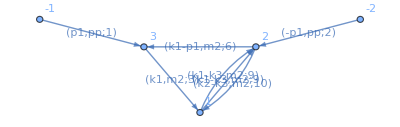

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6]) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.03846

```mathematica
toint=baik Pi^3 /(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
```

```mathematica
toint
```

-1/(x5 √(-pp^2-x5^2+2 pp (2+x5)) √(-4+x6) √x6 √(-(x5-x6)^2+4 x6))

```mathematica
(* the max cut of this graph contains the banana structure and an extra pole. Localizing on the pole, you get the max cut leading singularity. *)
maxcutBananatmp=K3Banana /. {x5 -> X6, x6 ->x5} /. X6 ->x6 //PowerExpand// FullSimplify//PowerExpand
integrand=toint /. x5 -> x5 -1//PowerExpand//FullSimplify//PowerExpand
```

x1/(√(pp^2+(-1+x5)^2-2 pp (1+x5)) √(-4+x6) √x6 √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

-1/((-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

```mathematica
(* the residue in x5 around 1*)
```

```mathematica
Integrate[PowerExpand[integrand (x5 - 1) /. x5 -> 1 ]//FullSimplify//PowerExpand,x6];
Coefficient[%,Log[x6]]
```

-1/(4 √(-4+pp) √pp)

```mathematica
(*
What are the other integrals?  They are not dlog forms and they are telling us about subpotologies. (in fact max cut is x5 -> 0 )
*)
```

```mathematica
(* Expand in pp to select the holomorphic solution *)
```

```mathematica
periodBanana=ω0[ρ]/.Import["./periods/k3_banana_3l/periods_0.m"][[1]];
```

```mathematica
toexpand =integrand (-I)16 √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2)(-1+x5) /. 1/Sqrt[a_]:> 1/Sqrt[-a]//FullSimplify//PowerExpand
seriestmp=  Collect[Collect[(Series[toexpand , {pp,0,25}]//Normal // PowerExpand) , {pp},Simplify]/(-1+x5), {pp}] ;
```

(16 ⅈ)/(√(pp^2+(-1+x5)^2-2 pp (1+x5)))

```mathematica
(*tmps1=Collect[(Series[-1/2Log[4 x6-(1-x5+x6)^2]+1/2Log[-((-4+x6) x6)], {x5,1,120}]//Normal)/.x5 -> x5m1 +1, {x5m1},Simplify];*)
```

```mathematica
(*E^(tmps1)/Sqrt[4-x6]/Sqrt[x6] /. {x5m1 -> 0.01, x6 ->1/2}
toexpandAgain=E^(tmps1);
tocheck=Normal[Series[toexpandAgain, {x5m1,0,50}]]/Sqrt[4-x6]/Sqrt[x6];*)
(*N[tocheck/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[expandRoot /.x5 -> x5m1 +1/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[1/√(4 x6-(1-x5+x6)^2) /. {x5 ->x5m1 +1}/. {x5m1 -> 10^-20, x6 ->1/2},40]*)
```

```mathematica
(*Export["./expandroots/expandroots.m",tocheck];*)
expandRoot= Import["./expandroots/expandroots.m"];
```

```mathematica
Print["done"]
(*Series and max cut do not commute *)
tmp=Residue[Series[ I seriestmp/√(4 x6-(1-x5+x6)^2)/. 1/√(4 x6-(1-x5+x6)^2) -> expandRoot /. x5m1 ->x5-1  , {x5,1,-1}],{x5,1}]//PowerExpand//Simplify;
function=(Residue[Series[tmp/√(4-x6)/Sqrt[x6],{x6,0,-1}, Assumptions->{x6 >0}]//Normal, {x6,0}]//Expand) /. pp ->ρ;
```

done

```mathematica
function=Expand[function F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
function/.extractPolySol /. ρ^a_ /; a> 5 -> 0
Series[--I/(4  √(-4+pp) √pp), {pp,0,5}, Assumptions->{Im[pp]>0}]//Normal
```

1+ρ/4+(61 ρ^2)/1024+(29 ρ^3)/2048+(14179 ρ^4)/4194304+(6803 ρ^5)/8388608

1/(8 √pp)+(√pp)/64+(3 pp^(3/2))/1024+(5 pp^(5/2))/8192+(35 pp^(7/2))/262144+(63 pp^(9/2))/2097152

```mathematica
periodBanana=Expand[periodBanana F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
(* second derivative of period not needed *)
maxorder=2
ansatzDer=Sum[a[i] ρ^i F1[], {i,1,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,1,maxorder}] ;
inhomog=   Sum[c[i]ρ^i , {i,1,maxorder}]F1[] periodBanana+  Sum[d[i]ρ^i , {i,1,maxorder}]F1[](Expand[D[periodBanana /. extractPolySol,ρ] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ /. F2[]  -> F2[g[ρ,0]])//Expand;
```

2

```mathematica
(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand;
```

```mathematica
sol=Equal[CoefficientList[(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand,ρ,15],0]//Solve//Flatten
```

{a[2]→-a[1]/2,b[1]→2 a[1],b[2]→-a[1]/2,c[1]→-a[1],c[2]→0,d[1]→0,d[2]→-3 a[1]}

```mathematica
ansatzDersol=ansatzDer /. sol  /. F1[]-> 1 /. a[1]-> 1
inhomogSol=Sum[c[i]ρ^i , {i,1,maxorder}] ω0+  Sum[d[i]ρ^i , {i,1,maxorder}] dω0/. sol  /. F1[]-> 1 /. a[1]-> 1
```

ρ-ρ^2/2+2 ρ F1[θ]-1/2 ρ^2 F1[θ]

-3 dω0 ρ^2-ρ ω0

```mathematica
(* the differential equation is *)
(*Solve[ρ F-ρ^2/2 F+2 ρ ρ derF-1/2 ρ^2 ρ derF  +-3 dω0 ρ^2-ρ ω0 == 0,derF]*)
(* 
derF->(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ)
*)
```

```mathematica
(*the canonical candidate is given by 

(-2+d) √(-((-4+ρ) ρ)) INT[topoB,1,1,0,1,0,0,1,1,0]+1/2 (-2+d) INT[topoB,0,1,0,1,0,0,1,1,0] ((3 √ρ)/(√(4-ρ))-G3[ρ]/ω0[ρ])

*)
```

```mathematica
(* Normalize by leading singularity on max cut, it remove the F *)
```

```mathematica
(*
integrating the homogeneous part, is equivalent to integrating 
E^(-Integrate[Coefficient[(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ),F],ρ])*)
```

```mathematica
Collect[D[√((4-ρ) ρ) F[ρ]-(6 ω0[ρ] ρ)/(√(-((-4+ρ) ρ))),ρ] /.F'[ρ]-> (2 F[ρ]-6 dω0 ρ-F[ρ] ρ-2 ω0)/((-4+ρ) ρ)  /. F[ρ] -> F[ρ]/√((4-ρ) ρ)/. {ω0[ρ] -> ω0, ω0'[ρ] -> dω0}, {_F,ω0,dω0},Simplify]
```

-(2 ρ (2+ρ) ω0)/(-((-4+ρ) ρ))^(3/2)

```mathematica
G3'[ρ]->((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)
(* so the correction can be obtained by removing F/omega0 banana, I need something that gives me a non trivial thing along that contour (the one that gives me the holomorphic solution ) *)
```

G3'[ρ]→((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)

## 3 loop Triangle sunrise dlog (G operator derived) pp -> inf

```mathematica
K3Banana=x1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6]) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.04176

```mathematica
toint=baik Pi^3 /(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
integrand=toint /. x5 -> x5 -1//PowerExpand//FullSimplify//PowerExpand
(* the residue in x5 around 1*)
Integrate[PowerExpand[integrand (x5 - 1) /. x5 -> 1 ]//FullSimplify//PowerExpand,x6];
Coefficient[%,Log[x6]]  /. pp -> 1/z // FullSimplify
```

-1/((-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

-z/(4 √(1-4 z))

```mathematica
Series[z/(√(1-4 z)), {z,0,3}]
```

z+2 z^2+6 z^3+O[z]^4

```mathematica
(*
What are the other integrals?  They are not dlog forms and they are telling us about subpotologies. (in fact max cut is x5 -> 0 )
*)
```

```mathematica
(* Expand in pp to select the holomorphic solution *)
```

```mathematica
periodBanana=ω0[ρ]/.Import["./periods/k3_banana_3l/periodsInf.m"][[1]];
```

```mathematica
toint=baik Pi^3 /(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
integrand = toint;
```

```mathematica
integrand=integrand /. pp -> 1/z /. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand//FullSimplify;
toexpand =integrand /. 1/Sqrt[a_]:> 1/Sqrt[-a]//FullSimplify//PowerExpand
```

z/(x5 √((x5-x6)^2-4 x6) √(4-x6) √x6 √(-1+z (4+x5 (2-x5 z))))

```mathematica
(*max cut*)
series=(Series[toexpand , {z,0,15},Assumptions->Im[(4+2 x5) z-x5^2 z^2]≥0]//Normal // PowerExpand) ;
series2 =Residue[ Series[series,{x5,0,-1}]//Normal // PowerExpand, {x5,0}];
series3=Series[(series2 )/. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand, {x6,0,-1}, Assumptions->Im[x6]≥0]//Normal;
functionToGuess=Residue[series3 (-4),{x6,0}]
```

z+2 z^2+6 z^3+20 z^4+70 z^5+252 z^6+924 z^7+3432 z^8+12870 z^9+48620 z^10+184756 z^11+705432 z^12+2704156 z^13+10400600 z^14+40116600 z^15

```mathematica
(*max cut*)
series=(Series[toexpand , {z,0,15},Assumptions->Im[(4+2 x5) z-x5^2 z^2]≥0]//Normal // PowerExpand) ;
series2 =Residue[ Series[(series /. x5 ->1/x5)/x5/x5,{x5,0,-1}]//Normal // PowerExpand, {x5,0}];
series3=Series[(series2  /. x6 -> 1/x6)/x6/x6/. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand, {x6,0,-1}, Assumptions->Im[x6]≥0]//Normal;
functionToGuess=Residue[-series3 ,{x6,0}];
```

```mathematica
function=Expand[(functionToGuess /. z ->ρ )  F2[]] /. F2[]ρ^n_ :>  F2[g[ρ,n]]
```

F2[g[ρ,2]]+8 F2[g[ρ,3]]+64 F2[g[ρ,4]]+576 F2[g[ρ,5]]+5876 F2[g[ρ,6]]+66176 F2[g[ρ,7]]+798848 F2[g[ρ,8]]+10113536 F2[g[ρ,9]]+132410764 F2[g[ρ,10]]+1777039008 F2[g[ρ,11]]+24307857344 F2[g[ρ,12]]+337590162432 F2[g[ρ,13]]+4747089191872 F2[g[ρ,14]]+67448190921728 F2[g[ρ,15]]

```mathematica
periodBanana = Import["./periods/k3_banana_3l/periodsInf.m"][[1,2]];
```

```mathematica
op1=ρ-1/2-2ρ F1[θ]+1/2  F1[θ]
inhomg=-3 ρ^2 dω0 +ρ ω0
```

-1/2+ρ+F1[θ]/2-2 ρ F1[θ]

-3 dω0 ρ^2+ρ ω0

```mathematica
Expand[op1 G ]+ inhomog
```

-G/2+G ρ-3 dω0 ρ^2+ρ ω0+1/2 G F1[θ]-2 G ρ F1[θ]

```mathematica
(4 op1 function  // Expand)/.combineOperator //. moveRightPoly //. extractPoly /. zeroOP /. F[]-> 1 
(-3 ρ^2 D[periodBanana ,ρ]+ρ periodBanana //Expand) /. ρ^n_ /; n> 12 -> 0
%%+%
```

2 ρ^2+20 ρ^3+224 ρ^4+2816 ρ^5+38024 ρ^6+535568 ρ^7+7742720 ρ^8+113885696 ρ^9+1695673304 ρ^10+25477562096 ρ^11+385501584896 ρ^12+5865841022720 ρ^13+89665302745472 ρ^14+1375863713086208 ρ^15-7823990146920448 ρ^16

-2 ρ^2-20 ρ^3-224 ρ^4-2816 ρ^5-38024 ρ^6-535568 ρ^7-7742720 ρ^8-113885696 ρ^9-1695673304 ρ^10-25477562096 ρ^11-385501584896 ρ^12

5865841022720 ρ^13+89665302745472 ρ^14+1375863713086208 ρ^15-7823990146920448 ρ^16

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
op1=(ρ-1/2-2ρ F1[θ]+1/2  F1[θ])
inhomog=-3 ρ^2 dω0 +ρ ω0
```

-1/2+ρ+F1[θ]/2-2 ρ F1[θ]

-3 dω0 ρ^2+ρ ω0

```mathematica
operator=Collect[(ρ G[ρ]-1/2 G[ρ]-2ρ ρ D[G[ρ],ρ]+1/2  ρ  D[G[ρ],ρ])   +-3 ρ^2 D[π0[ρ],ρ] +ρ π0[ρ], {_π0, _G},Simplify]
```

(-1/2+ρ) G[ρ]+ρ π0[ρ]-1/2 ρ ((-1+4 ρ) G'[ρ]+6 ρ π0'[ρ])

```mathematica
Solve[(-1/2+ρ) G[ρ]+ρ π0[ρ]-1/2 ρ ((-1+4 ρ) G'[ρ]+6 ρ π0'[ρ]) == 0, G'[ρ]]
```

{{G'[ρ]→(-G[ρ]+2 ρ G[ρ]+2 ρ π0[ρ]-6 ρ^2 π0'[ρ])/(ρ (-1+4 ρ))}}

```mathematica
leadingsing=DSolve[(-1/2+ρ) G[ρ]-1/2 ρ ((-1+4 ρ) G'[ρ])== 0,G[ρ],ρ]/.C[1]-> 1//Flatten
```

{G[ρ]→ρ/(√(1-4 ρ))}

```mathematica
D[1/(ρ/(√(1-4 ρ)))G[ρ],ρ]   /.G'[ρ]->(-G[ρ]+2 ρ G[ρ]+2 ρ π0[ρ]-6 ρ^2 π0'[ρ])/(ρ (-1+4 ρ))/.   G[ρ] -> nG[ρ]/(ρ/(√(1-4 ρ))) //Simplify
Collect[D[G[ρ],ρ]  -(-(2 (π0[ρ]-3 ρ π0'[ρ]))/(√(1-4 ρ) ρ)), {_G, _π0}, Simplify]
```

-(2 (π0[ρ]-3 ρ π0'[ρ]))/(√(1-4 ρ) ρ)

(2 π0[ρ])/(√(1-4 ρ) ρ)+G'[ρ]-(6 π0'[ρ])/(√(1-4 ρ))

```mathematica
Solve[(2 π0[ρ])/(√(1-4 ρ) ρ)+G'[ρ]-(6 π0'[ρ])/(√(1-4 ρ)) == 0,G'[ρ]]
```

{{G'[ρ]→(2 (-π0[ρ]+3 ρ π0'[ρ]))/(√(1-4 ρ) ρ)}}

```mathematica
Collect[D[G[ρ] -  (6  π0[ρ])/(1-4 ρ)^(1/2),ρ]  /. {G'[ρ]->(2 (-π0[ρ]+3 ρ π0'[ρ]))/(√(1-4 ρ) ρ)} /.  G[ρ] -> G[ρ] +  (6 ρ^2 π0[ρ])/(1-4 ρ)^(3/2),  {_G, _π0}, Simplify]
```

```mathematica
-((2+4 ρ) π0[ρ])/((1-4 ρ)^(3/2) ρ)//Factor
```

-(2 (1+2 ρ) π0[ρ])/((1-4 ρ)^(3/2) ρ)

```mathematica
(*Gfinal = (√(1-4 ρ))/ρ Gstart - (6  π0[ρ])/(1-4 ρ)^(1/2)*)
(* D[Gfinal[ρ],ρ]  = -((2+4 ρ) π0[ρ])/((1-4 ρ)^(3/2) ρ) *)
```

## 3 loop triangle bubble - bubble (G derived) (written)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik (32 π^(5/2) Gamma[1/2 (1-2 eps)] Gamma[-eps]^2) /((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6] x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik= baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-Graphics-,-Graphics-}

"Total runtime= "  0.062188

-((8 ⅈ √(3-pp^2-x1^2+4 x4-4 x6+2 x7+2 x1 (1+2 x4-2 x6+x7-2 x8)-4 x8-(-2 x6+x7+2 x8)^2+2 pp (1+x1-2 x6+x7+2 x8)))/((pp^2 (1+x4)+(1+x4) (1+x1-x7)^2+4 x6 (1+x1-x7) x8+4 x7 x8^2-2 pp (1+x1+x4+x1 x4+x7+x4 x7+2 x6 (-x6+x8))) (-2-x2+x2^2+pp^2 (1+x2)-x3-x2 x3+x3^2+x1^2 (1+x3)-2 x4-x2 x4+x2^2 x4-2 x3 x4+x4^2-x5-x2 x5-x3 x5-x4 x5-2 x2 x4 x5+x5^2+x4 x5^2+2 x6+2 x2 x6+2 x3 x6-2 x2 x3 x6-2 x4 x6+2 x2 x4 x6+2 x2 x5 x6+2 x3 x5 x6-2 x4 x5 x6-2 x5^2 x6+4 x6^2+4 x5 x6^2-x7-x2 x7-x3 x7+x2 x3 x7+x4 x7-x2 x4 x7-x2 x5 x7-x3 x5 x7+x4 x5 x7+x5^2 x7-4 x6 x7-4 x5 x6 x7+x7^2+x5 x7^2-x1 (1-x3^2+2 x4+x2 (1+x3+x4-x5)+x5-2 x6+x7-(x4-x5) (x4-2 x6+x7)+x3 (2 x4+x5-2 x6+x7))+2 x1 (1+x2+x3-x4+2 x6-x7) x8+2 (1-x2^2+x3-x4+x5-2 x6+x7+x5 (-x3+x4-2 x6+x7)+x2 (x3-x4+x5-2 x6+x7)) x8+4 (1+x2) x8^2-pp (1-x2^2+x3-x4+x5-2 x6+x1 (1+x2+x3-x4+2 x6-x7)+x7+x5 (-x3+x4-2 x6+x7)+4 x8+x2 (x3-x4+x5-2 x6+x7+4 x8)))))

```mathematica
(* First two loops, two loop sunrise, loop momenta k3, k4 *)
(*  P1 = p1+k1 
(k3)^2-m2, , (k3 + P1)^2-m2
*)
propfirstloop={sp[k3,k3]-m2,
sp[k3,k3] + pp + k1k1 + 2 k1p1 +2 sp[k3,P1]-m2}
(**)
sps= Union@Cases[propfirstloop,_sp,∞];
(*physical props are x1, x2, x3*)
isptoprop=Solve[Thread[Equal[propfirstloop , {x1,x2}]],sps]//Flatten;
```

{-m2+sp[k3,k3],k1k1+2 k1p1-m2+pp+sp[k3,k3]+2 sp[k3,P1]}

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
external = {P1};
allmomenta = {P1,k3};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=%/. sp[P1,P1]-> pp + k1k1 + 2 k1p1/. isptoprop//Simplify;
baik=detInternalMomenta^((d-1-1-1)/2); (* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det ;
mat2 =mat2/. sp[P1,P1]-> pp + k1k1 + 2 k1p1;
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop ;
baik=baik  detExternalMomenta^((2-d)/2) ;(* (1+E-d)/2 , E independent external momenta *)
firstLoopBaik = baik;
```

```mathematica
firstLoopBaik/. d->5//Variables
```

{k1k1,k1p1,m2,pp,x1,x2}

```mathematica
propsecondloop={sp[k1,k1]-m2,
sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,
(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x3,x4,x40}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x3,sp[k1,k2]→-k2k2/2-x3/2+x4/2,sp[k1,p1]→-m2/2-pp/2-x3/2+x40/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
Solve[sp[k1,k1]==m2+x3,x3]
```

{{x3→-m2+sp[k1,k1]}}

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]}/.isptoprop;
secondLoopBaik =baik2/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik/.d-> 20//Variables
```

{k2k2,k2p1,m2,pp,x3,x4,x40}

```mathematica
(*
k2^2, and isp k2.p1, bubble kinematics
*)
propthirdloop={sp[k2,k2]-m2,sp[k2,p1]}
isptoprop=Thread[Equal[propthirdloop , {x5,x41}]]//Solve//Flatten
external = {p1};
allmomenta = {p1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp/. isptoprop;
baik2=detInternalMomenta^((d-1-1-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. isptoprop 
baik2=baik2  detExternalMomenta^((1+1-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
thirdLoopBaik = baik2;
```

{-m2+sp[k2,k2],sp[k2,p1]}

{sp[k2,k2]→m2+x5,sp[k2,p1]→x41}

sp[p1,p1]

pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik  = secondLoopBaik/. {k2k2 -> sp[k2,k2], k2p1-> sp[k2,p1]}/.isptoprop;
(*physical props are x1, x2, x3, x4,x5,x6*)
baik = firstLoopBaik secondLoopBaik thirdLoopBaik /. {x40-> x7,x41->x8,x42->x9,x43->x10} /. m2->1;
Variables[baik/. d-> 2]
```

{pp,x1,x2,x3,x4,x5,x7,x8}

```mathematica
isptoprop
```

{sp[k2,k2]→m2+x5,sp[k2,p1]→x41}

```mathematica
baikd2=firstLoopBaik secondLoopBaik thirdLoopBaik /. d->2 /. m2-> 1//FullSimplify
```

-(8/(√(-(x1-x2)^2+2 (2+x1+x2) x40-x40^2) (1-2 x40+x40^2-2 x41+2 x4 x41+2 x40 x41-2 x4 x40 x41+4 x41^2+(-1+x40) (-1+x40+2 x41) x5+pp^2 (1+x5)+x3^2 (1-2 x41+x5)+2 x3 (1+x40 (-1+x41-x5)+x41 (-2+x4+2 x41-x5)+x5)+pp (-1+x3^2-2 x40-2 x41-2 x3 (x4+x41)+x4 (-2+x4+2 x41)-2 (x4+x40+x41) x5+x5^2))))

```mathematica
maxcut = baikd2 /. {x1->0,x2-> 0,x3->0,x4->0,x5->0}//FullSimplify;
```

```mathematica
int1=Integrate[maxcut,x41]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand
```

-4/(√3 √(-4+x40) √x40 √(pp^2+(-1+x40)^2-2 pp (1+x40)))

```mathematica
-4/(√3 √(-4+x40) √x40 √(pp^2+(-1+x40)^2-2 pp (1+x40)))/. x40 -> x6
```

-4/(√3 √(-4+x6) √x6 √(pp^2+(-1+x6)^2-2 pp (1+x6)))

```mathematica
(*MAX CUT, sunrise 2 loop, elliptic *)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand;
(Series[toint /. pp -> pp, {pp,0,5}]//Normal//PowerExpand);
Residue[Normal[Series[% 3 /4 I, {x6,1,-1},Assumptions->Im[x6]<0]],{x6,1}]//Expand
Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]/.ρ^n_ /; n> 3 ->0
```

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243

```mathematica
(*MAX CUT, taking x6 -> 1/x6, it cannot change *)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand;
(Series[toint /. pp -> pp, {pp,0,5}]//Normal//PowerExpand) ;
Residue[Series[Collect[(%  3 /4 I/. x6 -> 1/x6)/x6/x6, {pp}, FullSimplify], {x6,1,-1},Assumptions->Im[x6]≤0]//Normal, {x6,1}]//Expand
```

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

```mathematica
(*MAX CUT at inf,  sunrise 2 loop, elliptic *)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand;
(Series[toint /. pp -> 1/s, {s,0,5}]//Normal//PowerExpand)
(% /. x6 -> 1/x6)/x6/x6//FullSimplify;
Residue[Normal[Series[-% Sqrt[3] /4 , {x6,0,-1},Assumptions->Im[x6]<0]],{x6,0}]//Expand
```

-(4 s)/(√3 √(-4+x6) √x6)-(4 s^2 (1+x6))/(√3 √(-4+x6) √x6)-(4 s^3 (1+4 x6+x6^2))/(√3 √(-4+x6) √x6)-(4 s^4 (1+x6) (1+8 x6+x6^2))/(√3 √(-4+x6) √x6)-(4 s^5 (1+16 x6+36 x6^2+16 x6^3+x6^4))/(√3 √(-4+x6) √x6)

s+3 s^2+15 s^3+93 s^4+639 s^5

```mathematica
(*Expand around MUM point for the subcut, this is a K3*)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/x3/. {x1-> 0,x2-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]]
```

4/(√(-3+x3) x3 √(1+x3) √(-((-4+x6) x6)) √(pp^2+(1+x3-x6)^2-2 pp (1+x3+x6)))

```mathematica
(* max cut*)
toint2=toint /. pp ->1/z /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand;
tmp=Series[toint2, {z,0,5}]//Normal//Together;
tmp=Residue[Series[(tmp /. x6 ->1/x6)/x6/x6, {x6,0,-1}]//Normal, {x6,0}];
Residue[Normal[Series[-tmp Sqrt[3]/4, {x3,0,-1},Assumptions->Im[x3]>0]], {x3,0}]//Expand
```

z+3 z^2+15 z^3+93 z^4+639 z^5

```mathematica
(* second solution*)
Residue[Normal[Series[((I)tmp /4 /. x3 ->1/x3)/x3/x3, {x3,0,-1},Assumptions->Im[x3]>0]], {x3,0}]//Expand
```

z^2+11 z^3+117 z^4+1285 z^5

```mathematica
(*Expand around MUM point for the subcut, banana K3*)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]];
toint2=toint /. pp ->1/z /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand;
tmp=Series[toint2, {z,0,5}]//Normal//Together;
tmp=Residue[Series[(tmp /. x6 ->1/x6)/x6/x6, {x6,0,-1}]//Normal, {x6,0}]
Residue[Normal[Series[(I tmp /4 /. x3 -> 1/x3)/x3/x3, {x3,0,-1},Assumptions->Im[x3]>0]], {x3,0}]//Expand
```

-(4 ⅈ (z+3 z^2+x3 z^2+15 z^3+10 x3 z^3+x3^2 z^3+93 z^4+93 x3 z^4+21 x3^2 z^4+x3^3 z^4+639 z^5+852 x3 z^5+318 x3^2 z^5+36 x3^3 z^5+x3^4 z^5))/(√(-3+x3) √(1+x3))

z+4 z^2+28 z^3+256 z^4+2716 z^5

### Differential Operator at z -> ∞

```mathematica
(*Expand around MUM point for the subcut, this is a K3*)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/x3/. {x1-> 0,x2-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]];
toint2=toint /. pp ->1/s /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand// Simplify
```

-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3) √(-4+x6) √x6 √(1+s^2 (1+x3-x6)^2-2 s (1+x3+x6)))

```mathematica
toint2 √(1+s^2 (1+x3-x6)^2-2 s (1+x3+x6))√(-4+x6) √x6
```

-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3))

```mathematica
(*tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[1+s^2 (1+x3-x6)^2-2 s (1+x3+x6)], {s,0,60}]]), {s,0,50}]//Normal, {s}, Factor];
series=Series[((1/(√(-4+x6) √x6)/. x6 -> 1/x6)/x6/x6 // FullSimplify)(tmpsqrt/. x6 ->1/x6),{x6,0,-1}]//Normal;
num=Collect[Coefficient[series,x6,-1], {s},Simplify];*)
```

```mathematica
(*(* this is actually the max cut ...*)
function1=Residue[Series[(4 ⅈ s)/(√(-3+x3) x3 √(1+x3))num /4 Sqrt[3], {x3, 0,-1}, Assumptions->Im[x3]≥0]//Normal, {x3,0}]/.s-> z//Expand;*)
```

```mathematica
(*(* this is a new function instead.*)
function2=Residue[Series[(((4 ⅈ s)/(√(-3+x3) x3 √(1+x3))/(ⅈ √3)/. x3 -> 1/x3 )/x3/x3 // FullSimplify)(num /4 Sqrt[3] /. x3 -> 1/x3), {x3, 0,-1}, Assumptions->Im[x3]≥0]//Normal, {x3,0}]/.s-> z//Expand;*)
```

$Aborted

```mathematica
(*Export["./2loopHard/gfunctionExpansion_50orders.m",function2]*)
```

./2loopHard/gfunctionExpansion_50orders.m

```mathematica
banana3loopinf = Import["./periods/k3_banana_3l/periodsInf.m"][[1,2 ]];
sunriseatinf = Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2 ]];
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

```mathematica
functionToGuess = Import["./2loopHard/gfunctionExpansion_50orders.m"];
```

```mathematica
maxorderPoly = 5;
maxDerDer= 2;
maxDerInhom = 3;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer];
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana3loopinf];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)];
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,40],0]]]//Flatten;
```

```mathematica
sol = Join[sol /. {Subscript[a, 0,0]->0, Subscript[a, 0,1]->1, Subscript[b, 0,0]-> 0}, {Subscript[a, 0,0]->0, Subscript[a, 0,1]->1, Subscript[b, 0,0]-> 0}];
```

```mathematica
Collect[derOp/.sol  /. F1[] -> 1, {_F1},Factor]
inhomogFormal /. sol //Simplify
```

-ρ (-1+3 ρ)+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ]

1/2 ρ^2 (-f[ρ]+ρ ((-1+10 ρ) f'[ρ]+5 ρ (-1+2 ρ) f''[ρ]))

```mathematica
sunriseatinf1=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[2,2]];
sunriseatinf=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2]];
(*the homogenous part is just the sunrise operator, so it should annihilates the sunrise period, in fact..*)
toapplyto=Expand[sunriseatinf F2[]] /. z -> ρ /. F2[]ρ^n_ :> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]];
((-ρ (-1+3 ρ)+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ] )toapplyto // Expand)//.combineOperator //. moveRightPoly /.zeroOP  //.extractPoly /.zeroOP  /. ρ^n_ /; n > 150 -> 0
(*the homogenous part is just the sunrise operator, so it should annihilates the sunrise period, in fact..*)
toapplyto=Expand[sunriseatinf1] /. z -> ρ /. {Log[ρ]^m_  ρ^n_ :>  F2[g[log,m],g[ρ,n]],Log[ρ]^m_  ρ :>  F2[g[log,m],g[ρ,1]],Log[ρ]^m_ :> F2[g[log,m]],Log[ρ]ρ^n_ :> F2[g[log,1],g[ρ,n]],Log[ρ]ρ :> F2[g[log,1],g[ρ,1]],Log[ρ]->F2[g[log,1]],ρ^n_:> F2[g[ρ,n]] , ρ:> F2[g[ρ,1]]};
(((-ρ (-1+3 ρ)+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ] )toapplyto // Expand)//.combineOperator//.moveRightLog  //. moveRightPoly  //.extractPoly //.zeroOP //Expand) /. ρ^n_ /; n > 150 -> 0 /. F[]-> 1/. ρ^n_ /; n > 10 -> 0// Simplify
```

0

0

```mathematica
(*maxorderPoly = 5;
maxDerDer= 1;
maxDerInhom = 3;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), (banana3loop (sunriseatinf) /. z ->ρ)];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog ], ρ,20],0]]]//Flatten*)
```

#### simplify eqs.

```mathematica
sunriseatinf1=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[2,2]];
sunriseatinf=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2]];
```

```mathematica
-((D[sunriseatinf  ,ρ](Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[2,2]])- D[Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[2,2]],ρ]sunriseatinf//Simplify)(1-10 ρ+9 ρ^2)/ρ//Expand) /. ρ^n_ /; n> 140 -> 0
Δ =z/(1-10 z+9 z^2)
```

1

z/(1-10 z+9 z^2)

```mathematica
ρ d/dρ (ρ d/dρ) = ρ
```

```mathematica
-ρ (-1+3 ρ)+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ]
```

```mathematica
(-1+ρ) ρ (-1+9 ρ)ρ^2
```

```mathematica
Series[D[(functionToGuess / sunriseatinf /. ρ-> z),z], {z,0,2}]
```

1+16 z+234 z^2+O[z]^3

```mathematica
Series[(sunriseatinf^2 /. ρ ->z)/Δ D[(functionToGuess / sunriseatinf /. ρ-> z),z], {z,0,40}]//Normal;
D[%,z] /. z^n_ /; n> 10 -> 0
Series[sunriseatinf  (1/2 ρ^2 ( 1/((-1+ρ) ρ (-1+9 ρ)ρ^2) )(-banana3loopinf+ρ ((-1+10 ρ) D[banana3loopinf,ρ]+5 ρ (-1+2 ρ)  D[D[banana3loopinf,ρ],ρ])))/Δ/.ρ-> z, {z,0,10}]//Normal
```

```mathematica
(1/2 ρ^2 (-ban+ρ ((-1+10 ρ) banp+5 ρ (-1+2 ρ)  banpp)))
```

1/2 ρ^2 (-ban+ρ (5 banpp ρ (-1+2 ρ)+banp (-1+10 ρ)))

```mathematica
(*(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1,  ω1/ω0},{0,1}}
Wss = {{ω0,0},{dω0,gtc/ω0}}
Wss.Wu /. repl//Simplify*)
```

```mathematica
( {{ω0,0},{dω0,gtc/ω0}}//Inverse)
```

{{1/ω0,0},{-dω0/gtc,ω0/gtc}}

```mathematica
Series[-Integrate[Series[sunriseatinf   1/((-1+ρ) ρ (-1+9 ρ)ρ^2) (1/2 ρ^2 (-banana3loopinf+ρ ((-1+10 ρ) D[banana3loopinf,ρ]+5 ρ (-1+2 ρ)  D[D[banana3loopinf,ρ],ρ])))/Δ /.z->ρ, {ρ,0,20}]//Normal, ρ](sunriseatinf1 /. z-> ρ), {ρ,0,10}]//Normal
Series[Integrate[Series[sunriseatinf1    1/((-1+ρ) ρ (-1+9 ρ)ρ^2)   (1/2 ρ^2 (-banana3loopinf+ρ ((-1+10 ρ) D[banana3loopinf,ρ]+5 ρ (-1+2 ρ)  D[D[banana3loopinf,ρ],ρ])))/Δ /.z->ρ, {ρ,0,20}]//Normal,ρ](sunriseatinf /. z-> ρ), {ρ,0,10}]//Normal
Series[%%+%, {ρ,0,10}]//Normal
```

ρ^2 Log[ρ]+ρ^3 (4+15 Log[ρ])+ρ^4 (74+209 Log[ρ])+1/3 ρ^5 (3358+8733 Log[ρ])+ρ^6 (16121+41253 Log[ρ])+ρ^8 (3334115+8731189 Log[ρ])+1/15 ρ^7 (3463237+8932665 Log[ρ])+1/35 ρ^9 (1704888667+4535911905 Log[ρ])+1/70 ρ^10 (50381787251+135955761830 Log[ρ])

1/70 ρ^10 (-25228414181-135955761830 Log[ρ])+1/15 ρ^7 (-838972-8932665 Log[ρ])+ρ^8 (-1175566-8731189 Log[ρ])+ρ^4 (43-209 Log[ρ])+ρ^3 (7-15 Log[ρ])+ρ^2 (1-Log[ρ])-71/3 ρ^5 (-7+123 Log[ρ])-3 ρ^6 (474+13751 Log[ρ])-3/35 ρ^9 (247688814+1511970635 Log[ρ])

ρ^2+11 ρ^3+117 ρ^4+1285 ρ^5+14699 ρ^6+174951 ρ^7+2158549 ρ^8+27480635 ρ^9+359333901 ρ^10

## 4 loop banana (period verified with differential eq)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6] x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik =Pi^4  baik // FullSimplify;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.044486

```mathematica
maxcutIntegrand=baik /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} // FullSimplify // PowerExpand//FullSimplify
```

ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8)))

```mathematica
toint=-maxcutIntegrand /. pp ->1/s//FullSimplify//PowerExpand;
series=Collect[Series[toint, {s,0,5}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
tmp=Collect[tmp, {s}, Simplify];
(* Square root, so it has a pole a infinity in x7  *)
series=Collect[(tmp/. x7 ->1/x7)/x7/x7 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x7,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x7,0}];
tmp=Collect[tmp, {s}, Simplify];
(* Square root, so it has a pole a infinity in x6  *)
series=Collect[(tmp/. x6->1/x6)/x6/x6 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x6,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x6,0}];
tmp=Collect[tmp, {s}, Simplify]
periodsFourLoopBanana = Import["./periods/CY_3_banana_4l/periods.m"][[1,2]] /. ρ^n_ /; n>5 -> 0
Print[" Yeee "]
```

s+5 s^2+45 s^3+545 s^4+7885 s^5

ρ+5 ρ^2+45 ρ^3+545 ρ^4+7885 ρ^5

Yeee

## 4 loop triangle - sunrise easy (dlog?) (to do by hand)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^(-ν[6]) x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik = Pi^4 baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.047899

-1/(√(-pp^2-(x5-x6)^2+2 pp (2+x5+x6)) √(-(x1-x4)^2+2 (2+x1+x4) x7-x7^2) √(-(x3-x6)^2+2 (2+x3+x6) x8-x8^2) √(-(1+x2-x7)^2+2 (1+x2+x7) x8-x8^2))

```mathematica
(* max cut *)
toint=baik  /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0,x6-> 0}//FullSimplify // PowerExpand// FullSimplify
toint /.  x8 -> x8 -1
```

-ⅈ/(√(-4+pp) √pp √(-4+x7) √x7 √(-4+x8) √x8 √(-x7^2-(-1+x8)^2+2 x7 (1+x8)))

-ⅈ/(√(-4+pp) √pp √(-4+x7) √x7 √(-5+x8) √(-1+x8) √(-x7^2-(-2+x8)^2+2 x7 x8))

```mathematica
(*MAX CUT*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> pp, {pp,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Series[%,{x8,1,-1}, Assumptions->{Im[x8]>0}]//Normal//FullSimplify;
Print[" max cut in pp"]
Residue[%% I 4 Sqrt[3],{x8,1}]//Expand
(*MAX CUT at inf*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> 1/s, {s,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Collect[(% /. x8 -> 1/x8)/x8^2, {s}, FullSimplify];
Print[" max cut in s = 1 / pp"]
Residue[Series[%% 4, {x8,0,-1}]//Normal, {x8,0}]
```

max cut in pp

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

max cut in s = 1 / pp

s+3 s^2+15 s^3+93 s^4+639 s^5

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Collect[Series[toint, {s,0,3}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
Print["notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞"]
tmp=Collect[tmp, {s}, Simplify] // Together
 (*single pole for x6 -> 0, this goes to max cut*)
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[4 series2,{x6,0}];
(*put back the s*)
Print["this is again the max cut solution, found by taking the pole at 0 :) "]
Collect[s Residue[Series[- tmp2, {x7,0,-1}]//Normal, {x7,0}], {s},FullSimplify]
(* Stupid pole at infinity now !!!!! *)
Print[" by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !"]
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}]
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞

(ⅈ (1+3 s+15 s^2+93 s^3+s x6+10 s^2 x6+93 s^3 x6+s^2 x6^2+21 s^3 x6^2+s^3 x6^3))/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

this is again the max cut solution, found by taking the pole at 0 :)

s+3 s^2+15 s^3+93 s^4

by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !

(s^3+s^2 x6+21 s^3 x6+s x6^2+10 s^2 x6^2+93 s^3 x6^2+x6^3+3 s x6^3+15 s^2 x6^3+93 s^3 x6^3)/(x6^3 √(-4+x7) √x7 √(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2))

and this contour give the independent solution

s+12 s^2+145 s^3

```mathematica
(*(* this is correctly the banana, up to the new pole*)
bananaCut=baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
((bananaCut//PowerExpand//FullSimplify//PowerExpand) // Simplify//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
banana4loop=(ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8))) /. {x6 -> x7, x7 -> x6}/.x6 -> x6+1//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
%%/%*)
```

```mathematica
(*more ... *)
```

```mathematica
toint=baik x8/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,15}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

-1/((-4+x7) x7)2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

1/2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

```mathematica
(* derivative, second kind *)
```

```mathematica
toint=D[baik,pp] /x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,6}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

(s+6 s^2+45 s^3+372 s^4+3195 s^5+27918 s^6)/((-4+x7) x7)

1/4 (-s-6 s^2-45 s^3-372 s^4-3195 s^5-27918 s^6)

### Differential Operator at z -> ∞

```mathematica
toint
```

-ⅈ/(x6 √(-4+x7) √x7 √(-(x6-x7)^2+4 x7) √(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8)))

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

```mathematica
tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[-1-s^2 (-1+x8)^2+2 s (1+x8)], {s,0,130},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]<0]]), {s,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Collect[Series[1/(√(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,10},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]≥0], {s},Factor];
Series[tmpsqrt, {s,0,10}]//Normal;
%%+%//Together;*)
```

```mathematica
tmptoint=((toint √(-1-s^2 (-1+x8)^2+2 s (1+x8)) /. x8 ->1/x8)/x8/x8 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-4 x8-2 x6 x8+x6^2 x8^2) x8
```

-1/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

```mathematica
tmpsqrt2=Collect[Series[E^(-1/2 Normal[Series[Log[1-4 x8-2 x6 x8+x6^2 x8^2], {x8,0,140}]]), {x8,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Series[((Series[1/(√(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,3},Assumptions->Im[-s^2 (-1+x8)^2+2 s (1+x8)]>0]//Normal)/.x8-> 1/x8)/x8/x8 /. 1/Sqrt[a_]:>1/Sqrt[Factor[a]]//PowerExpand, {x8,0,-1}]//Normal
Collect[%,{s},Simplify]*)
```

```mathematica
num=Collect[Coefficient[Series[1/x8 tmpsqrt2 (tmpsqrt/.x8 -> 1/x8), {x8,0,-1}] // Normal , x8,-1], {s},Simplify];
```

```mathematica
tmptoint2=((tmptoint/. x6 -> 1/x6 )/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2);
tmpsqrt3=Collect[Series[E^(-1/2 Normal[Series[Log[1-2 x6 x7-4 x6^2 x7+x6^2 x7^2], {x6,0,140}]]), {x6,0,120}]//Normal, {s}, Factor];
num=Coefficient[Collect[Series[tmpsqrt3( num /. x6 -> 1/x6), {x6,0,-1}]//Normal, {s},Factor], x6,-1];
tmptoint3=Collect[((ⅈ/(√(-4+x7) √x7)/. x7 -> 1/x7)/x7/x7 /. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand)(num/. x7 -> 1/x7), {s},Normal[ Series[#, {x7,0,-1}, Assumptions->{x7 >4}]]&];
test=Residue[-I %,{x7,0}] /. s -> z;
test = test /. z^n_ /; n> 110 -> 0;
```

```mathematica
(*Export["./4loopEasy/gfunctionExpansion_110orders.m",test]*)
```

```mathematica
(*
series=Collect[Series[toint, {s,0,28}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together;
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
functionToGuess=Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}];
functionToGuess=functionToGuess /. s -> z *)
(*Export["./4loopEasy/gfunctionExpansion_28orders.m",functionToGuess]*)
```

```mathematica
functionToGuess=Import["./4loopEasy/gfunctionExpansion_110orders.m"];
```

```mathematica
ratio =Collect[Series[ Import["./periods/CY_3_banana_4l/periods.m"][[2,2]]/ Import["./periods/CY_3_banana_4l/periods.m"][[1,2]] /. Log[ρ]-> L,{ρ,0,100}]//Normal, {L},Simplify] /. L -> Log[ρ];
α1 = Series[1/(ρ D[ratio,ρ]),{ρ,0,100}]//Normal;
```

```mathematica
banana4loop = Import["./periods/CY_3_banana_4l/periods.m"][[1,2 ]];
```

```mathematica
banana=Expand[(banana4loop F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dbanana=Expand[(D[banana4loop,ρ]F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ddbanana=Expand[D[D[banana4loop,ρ],ρ]]F2[]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dddbanana=Expand[D[D[D[banana4loop,ρ],ρ],ρ]F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1f= Expand[α1 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ooα1= Expand[(Series[1/α1, {ρ,0,100}]//Normal) F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1fsquared= Expand[α1^2 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
```

```mathematica
maxorderPoly = 4;
maxDerDer= 2;
maxDerInhom = 2;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana4loop];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,70],0]]]//Flatten
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3)+ρ^4 a_(0,4))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3)+ρ^4 a_(1,4))+F1[θ,θ] (a_(2,0)+ρ a_(2,1)+ρ^2 a_(2,2)+ρ^3 a_(2,3)+ρ^4 a_(2,4))

f[ρ] b_(0,0)+b_(1,0) f'[ρ]+b_(2,0) f''[ρ]+ρ (f[ρ] b_(0,1)+b_(1,1) f'[ρ]+b_(2,1) f''[ρ])+ρ^2 (f[ρ] b_(0,2)+b_(1,2) f'[ρ]+b_(2,2) f''[ρ])+ρ^3 (f[ρ] b_(0,3)+b_(1,3) f'[ρ]+b_(2,3) f''[ρ])+ρ^4 (f[ρ] b_(0,4)+b_(1,4) f'[ρ]+b_(2,4) f''[ρ])

{a_(0,0)→0,a_(0,3)→-9 a_(0,1)-3 a_(0,2),a_(0,4)→0,a_(1,0)→0,a_(1,1)→(10 a_(0,1))/3,a_(1,2)→4 a_(0,1)+(10 a_(0,2))/3,a_(1,3)→-18 a_(0,1)-6 a_(0,2),a_(1,4)→0,a_(2,0)→-(a_(0,1))/3,a_(2,1)→(7 a_(0,1))/3-(a_(0,2))/3,a_(2,2)→7 a_(0,1)+(10 a_(0,2))/3,a_(2,3)→-9 a_(0,1)-3 a_(0,2),a_(2,4)→0,b_(0,0)→(a_(0,1))/10,b_(0,1)→(3 a_(0,1))/10+(a_(0,2))/10,b_(0,2)→0,b_(0,3)→0,b_(0,4)→0,b_(1,0)→0,b_(1,1)→(7 a_(0,1))/30,b_(1,2)→-(4 a_(0,1))/5+(7 a_(0,2))/30,b_(1,3)→-(9 a_(0,1))/2-(3 a_(0,2))/2,b_(1,4)→0,b_(2,0)→0,b_(2,1)→0,b_(2,2)→(7 a_(0,1))/10,b_(2,3)→(3 a_(0,1))/5+(7 a_(0,2))/10,b_(2,4)→-(9 a_(0,1))/2-(3 a_(0,2))/2}

```mathematica
sol=Join[sol/. { Subscript[a, 0,1]->1 ,   Subscript[a, 0,2]->1 },{ Subscript[a, 0,1]->1 ,   Subscript[a, 0,2]->1 }];
```

```mathematica
Collect[inhomogFormal/.sol//Simplify, {ρ},Simplify]
Collect[derOp/.sol//Simplify, {ρ},Simplify] /. F1[]-> 1
```

f[ρ]/10+ρ ((2 f[ρ])/5+(7 f'[ρ])/30)-6 ρ^4 f''[ρ]+ρ^3 (-6 f'[ρ]+(13 f''[ρ])/10)+1/30 ρ^2 (-17 f'[ρ]+21 f''[ρ])

-1/3 F1[θ,θ]-12 ρ^3 (1+2 F1[θ]+F1[θ,θ])+ρ (1+(10 F1[θ])/3+2 F1[θ,θ])+ρ^2 (1+(22 F1[θ])/3+31/3 F1[θ,θ])

```mathematica
Collect[derOp  /. sol , {_F1},Factor]
```

0

```mathematica
(* second derivative of period not needed ? *)
maxorder=5
ansatzDer=Sum[a[i] ρ^i F1[], {i,0,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,0,maxorder}](*+ Sum[c[i]F1[θ,θ] ρ^i, {i,1,maxorder}] + Sum[d[i]F1[θ,θ,θ] ρ^i, {i,1,maxorder}]+Sum[e[i]F1[θ,θ,θ,θ] ρ^i, {i,1,maxorder}]*) ;
inhomog=   Sum[f[i]ρ^i , {i,0,maxorder}]F1[] banana+  Sum[g[i]ρ^i , {i, 0,maxorder}]F1[]dbanana+Sum[h[i]ρ^i , {i, 0,maxorder}]F1[]ddbanana+Sum[ii[i]ρ^i , {i, 0,maxorder}]F1[]dddbanana+
Sum[l[i]ρ^i , {i, 0,maxorder}]F1[]α1+Sum[m[i]ρ^i , {i, 0,maxorder}]F1[]ooα1//Expand;
```

5

```mathematica
tmpfunctionToguess=(Expand[(functionToGuess F2[] /. z ->ρ)]/. ρ^n_ F2[] -> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]]);
sol=Equal[CoefficientList[(ansatzDer tmpfunctionToguess+inhomog // Expand) //. combineOperator //.moveRightPoly//.extractPoly /. zeroOP /. F[]-> 1 // PowerExpand,ρ,60],0]//Solve//Flatten
```

{a[0]→0,a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,b[0]→0,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,f[0]→0,f[1]→0,f[2]→0,f[3]→0,f[4]→0,f[5]→0,g[0]→0,g[1]→0,g[2]→0,g[3]→0,g[4]→0,g[5]→0,h[0]→0,h[1]→0,h[2]→0,h[3]→0,h[4]→0,h[5]→0,ii[0]→0,ii[1]→0,ii[2]→0,ii[3]→0,ii[4]→0,ii[5]→0,l[0]→0,l[1]→0,l[2]→0,l[3]→0,l[4]→0,l[5]→0,m[0]→0,m[1]→0,m[2]→0,m[3]→0,m[4]→0,m[5]→0}

```mathematica
operder=ansatzDer /. sol /. a[1] -> 1  
nhomog=   Sum[e[i]ρ^i , {i,1,maxorder}]F1[] ω0sunrise+  Sum[f[i]ρ^i , {i,0,maxorder}]F1[]dω0sunrise /. sol  /. a[1]-> 1//Expand
```

0

ρ ω0sunrise e[1] F1[]+ρ^2 ω0sunrise e[2] F1[]+ρ^3 ω0sunrise e[3] F1[]+ρ^4 ω0sunrise e[4] F1[]

## 4 loop triangle bubble - sunrise easy (elliptic) (G derived)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^(-ν[6]) x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik = Pi^4 baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

{-Graphics-,-Graphics-}

"Total runtime= "  0.051198

-1/(√(-(x1-x3)^2+2 (2+x1+x3) x7-x7^2) √(-(x2-x6)^2+2 (2+x2+x6) x7-x7^2) √(-(x4-x6)^2+2 (2+x4+x6) x8-x8^2) √(-pp^2-(1+x5-x8)^2+2 pp (1+x5+x8)))

```mathematica
(* max cut *)
toint=baik  /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0,x6-> 0}//FullSimplify // PowerExpand// FullSimplify
int1=Integrate[toint, x7];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]
```

-ⅈ/((-4+x7) x7 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

-ⅈ/(4 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

```mathematica
(*Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]/.ρ^n_ /; n> 3 ->0*)
```

```mathematica
(*MAX CUT*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> pp, {pp,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Series[%,{x8,1,-1}, Assumptions->{Im[x8]>0}]//Normal//FullSimplify;
Print[" max cut in pp"]
Residue[%% I 4 Sqrt[3],{x8,1}]//Expand
(*MAX CUT at inf*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> 1/s, {s,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Collect[(% /. x8 -> 1/x8)/x8^2, {s}, FullSimplify];
Print[" max cut in s = 1 / pp"]
Residue[Series[%% 4, {x8,0,-1}]//Normal, {x8,0}]
```

max cut in pp

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

max cut in s = 1 / pp

s+3 s^2+15 s^3+93 s^4+639 s^5

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Collect[Series[toint, {s,0,3}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
Print["notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞"]
tmp=Collect[tmp, {s}, Simplify] // Together
 (*single pole for x6 -> 0, this goes to max cut*)
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[4 series2,{x6,0}];
(*put back the s*)
Print["this is again the max cut solution, found by taking the pole at 0 :) "]
Collect[s Residue[Series[- tmp2, {x7,0,-1}]//Normal, {x7,0}], {s},FullSimplify]
(* Stupid pole at infinity now !!!!! *)
Print[" by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !"]
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}]
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞

(ⅈ (1+3 s+15 s^2+93 s^3+s x6+10 s^2 x6+93 s^3 x6+s^2 x6^2+21 s^3 x6^2+s^3 x6^3))/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

this is again the max cut solution, found by taking the pole at 0 :)

s+3 s^2+15 s^3+93 s^4

by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !

(s^3+s^2 x6+21 s^3 x6+s x6^2+10 s^2 x6^2+93 s^3 x6^2+x6^3+3 s x6^3+15 s^2 x6^3+93 s^3 x6^3)/(x6^3 √(-4+x7) √x7 √(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2))

and this contour give the independent solution

s+12 s^2+145 s^3

```mathematica
(*(* this is correctly the banana, up to the new pole*)
bananaCut=baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
((bananaCut//PowerExpand//FullSimplify//PowerExpand) // Simplify//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
banana4loop=(ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8))) /. {x6 -> x7, x7 -> x6}/.x6 -> x6+1//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
%%/%*)
```

```mathematica
(*more ... *)
```

```mathematica
toint=baik x8/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,15}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

-1/((-4+x7) x7)2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

1/2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

```mathematica
(* derivative, second kind *)
```

```mathematica
toint=D[baik,pp] /x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,6}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

(s+6 s^2+45 s^3+372 s^4+3195 s^5+27918 s^6)/((-4+x7) x7)

1/4 (-s-6 s^2-45 s^3-372 s^4-3195 s^5-27918 s^6)

### Differential Operator at z -> ∞

```mathematica
toint
```

-ⅈ/(x6 √(-4+x7) √x7 √(-(x6-x7)^2+4 x7) √(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8)))

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

```mathematica
tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[-1-s^2 (-1+x8)^2+2 s (1+x8)], {s,0,130},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]<0]]), {s,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Collect[Series[1/(√(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,10},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]≥0], {s},Factor];
Series[tmpsqrt, {s,0,10}]//Normal;
%%+%//Together;*)
```

```mathematica
tmptoint=((toint √(-1-s^2 (-1+x8)^2+2 s (1+x8)) /. x8 ->1/x8)/x8/x8 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-4 x8-2 x6 x8+x6^2 x8^2) x8
```

-1/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

```mathematica
tmpsqrt2=Collect[Series[E^(-1/2 Normal[Series[Log[1-4 x8-2 x6 x8+x6^2 x8^2], {x8,0,140}]]), {x8,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Series[((Series[1/(√(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,3},Assumptions->Im[-s^2 (-1+x8)^2+2 s (1+x8)]>0]//Normal)/.x8-> 1/x8)/x8/x8 /. 1/Sqrt[a_]:>1/Sqrt[Factor[a]]//PowerExpand, {x8,0,-1}]//Normal
Collect[%,{s},Simplify]*)
```

```mathematica
num=Collect[Coefficient[Series[1/x8 tmpsqrt2 (tmpsqrt/.x8 -> 1/x8), {x8,0,-1}] // Normal , x8,-1], {s},Simplify];
```

```mathematica
tmptoint2=((tmptoint/. x6 -> 1/x6 )/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2);
tmpsqrt3=Collect[Series[E^(-1/2 Normal[Series[Log[1-2 x6 x7-4 x6^2 x7+x6^2 x7^2], {x6,0,140}]]), {x6,0,120}]//Normal, {s}, Factor];
num=Coefficient[Collect[Series[tmpsqrt3( num /. x6 -> 1/x6), {x6,0,-1}]//Normal, {s},Factor], x6,-1];
tmptoint3=Collect[((ⅈ/(√(-4+x7) √x7)/. x7 -> 1/x7)/x7/x7 /. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand)(num/. x7 -> 1/x7), {s},Normal[ Series[#, {x7,0,-1}, Assumptions->{x7 >4}]]&];
test=Residue[-I %,{x7,0}] /. s -> z;
test = test /. z^n_ /; n> 110 -> 0;
```

```mathematica
(*Export["./4loopEasy/gfunctionExpansion_110orders.m",test]*)
```

```mathematica
(*
series=Collect[Series[toint, {s,0,28}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together;
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
functionToGuess=Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}];
functionToGuess=functionToGuess /. s -> z *)
(*Export["./4loopEasy/gfunctionExpansion_28orders.m",functionToGuess]*)
```

```mathematica
functionToGuess=Import["./4loopEasy/gfunctionExpansion_110orders.m"];
```

```mathematica
ratio =Collect[Series[ Import["./periods/CY_3_banana_4l/periods.m"][[2,2]]/ Import["./periods/CY_3_banana_4l/periods.m"][[1,2]] /. Log[ρ]-> L,{ρ,0,100}]//Normal, {L},Simplify] /. L -> Log[ρ];
α1 = Series[1/(ρ D[ratio,ρ]),{ρ,0,100}]//Normal;
```

```mathematica
banana4loop = Import["./periods/CY_3_banana_4l/periods.m"][[1,2 ]];
```

```mathematica
banana=Expand[(banana4loop F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dbanana=Expand[(D[banana4loop,ρ]F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ddbanana=Expand[D[D[banana4loop,ρ],ρ]]F2[]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dddbanana=Expand[D[D[D[banana4loop,ρ],ρ],ρ]F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1f= Expand[α1 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ooα1= Expand[(Series[1/α1, {ρ,0,100}]//Normal) F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1fsquared= Expand[α1^2 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

```mathematica
maxorderPoly = 4;
maxDerDer= 2;
maxDerInhom = 2;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana4loop];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,70],0]]]//Flatten
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3)+ρ^4 a_(0,4))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3)+ρ^4 a_(1,4))+F1[θ,θ] (a_(2,0)+ρ a_(2,1)+ρ^2 a_(2,2)+ρ^3 a_(2,3)+ρ^4 a_(2,4))

f[ρ] b_(0,0)+b_(1,0) f'[ρ]+b_(2,0) f''[ρ]+ρ (f[ρ] b_(0,1)+b_(1,1) f'[ρ]+b_(2,1) f''[ρ])+ρ^2 (f[ρ] b_(0,2)+b_(1,2) f'[ρ]+b_(2,2) f''[ρ])+ρ^3 (f[ρ] b_(0,3)+b_(1,3) f'[ρ]+b_(2,3) f''[ρ])+ρ^4 (f[ρ] b_(0,4)+b_(1,4) f'[ρ]+b_(2,4) f''[ρ])

{a_(0,0)→0,a_(0,3)→-9 a_(0,1)-3 a_(0,2),a_(0,4)→0,a_(1,0)→0,a_(1,1)→(10 a_(0,1))/3,a_(1,2)→4 a_(0,1)+(10 a_(0,2))/3,a_(1,3)→-18 a_(0,1)-6 a_(0,2),a_(1,4)→0,a_(2,0)→-(a_(0,1))/3,a_(2,1)→(7 a_(0,1))/3-(a_(0,2))/3,a_(2,2)→7 a_(0,1)+(10 a_(0,2))/3,a_(2,3)→-9 a_(0,1)-3 a_(0,2),a_(2,4)→0,b_(0,0)→(a_(0,1))/10,b_(0,1)→(3 a_(0,1))/10+(a_(0,2))/10,b_(0,2)→0,b_(0,3)→0,b_(0,4)→0,b_(1,0)→0,b_(1,1)→(7 a_(0,1))/30,b_(1,2)→-(4 a_(0,1))/5+(7 a_(0,2))/30,b_(1,3)→-(9 a_(0,1))/2-(3 a_(0,2))/2,b_(1,4)→0,b_(2,0)→0,b_(2,1)→0,b_(2,2)→(7 a_(0,1))/10,b_(2,3)→(3 a_(0,1))/5+(7 a_(0,2))/10,b_(2,4)→-(9 a_(0,1))/2-(3 a_(0,2))/2}

```mathematica
sol=Join[sol/. { Subscript[a, 0,1]->1 ,   Subscript[a, 0,2]->1 },{ Subscript[a, 0,1]->1 ,   Subscript[a, 0,2]->1 }];
```

```mathematica
Collect[inhomogFormal/.sol//Simplify, {ρ},Simplify]
Collect[derOp/.sol//Simplify, {ρ},Simplify] /. F1[]-> 1
```

f[ρ]/10+ρ ((2 f[ρ])/5+(7 f'[ρ])/30)-6 ρ^4 f''[ρ]+ρ^3 (-6 f'[ρ]+(13 f''[ρ])/10)+1/30 ρ^2 (-17 f'[ρ]+21 f''[ρ])

-1/3 F1[θ,θ]-12 ρ^3 (1+2 F1[θ]+F1[θ,θ])+ρ (1+(10 F1[θ])/3+2 F1[θ,θ])+ρ^2 (1+(22 F1[θ])/3+31/3 F1[θ,θ])

```mathematica
Collect[derOp  /. sol , {_F1},Factor]
```

0

```mathematica
(* second derivative of period not needed ? *)
maxorder=5
ansatzDer=Sum[a[i] ρ^i F1[], {i,0,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,0,maxorder}](*+ Sum[c[i]F1[θ,θ] ρ^i, {i,1,maxorder}] + Sum[d[i]F1[θ,θ,θ] ρ^i, {i,1,maxorder}]+Sum[e[i]F1[θ,θ,θ,θ] ρ^i, {i,1,maxorder}]*) ;
inhomog=   Sum[f[i]ρ^i , {i,0,maxorder}]F1[] banana+  Sum[g[i]ρ^i , {i, 0,maxorder}]F1[]dbanana+Sum[h[i]ρ^i , {i, 0,maxorder}]F1[]ddbanana+Sum[ii[i]ρ^i , {i, 0,maxorder}]F1[]dddbanana+
Sum[l[i]ρ^i , {i, 0,maxorder}]F1[]α1+Sum[m[i]ρ^i , {i, 0,maxorder}]F1[]ooα1//Expand;
```

5

```mathematica
tmpfunctionToguess=(Expand[(functionToGuess F2[] /. z ->ρ)]/. ρ^n_ F2[] -> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]]);
sol=Equal[CoefficientList[(ansatzDer tmpfunctionToguess+inhomog // Expand) //. combineOperator //.moveRightPoly//.extractPoly /. zeroOP /. F[]-> 1 // PowerExpand,ρ,60],0]//Solve//Flatten
```

{a[0]→0,a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,b[0]→0,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,f[0]→0,f[1]→0,f[2]→0,f[3]→0,f[4]→0,f[5]→0,g[0]→0,g[1]→0,g[2]→0,g[3]→0,g[4]→0,g[5]→0,h[0]→0,h[1]→0,h[2]→0,h[3]→0,h[4]→0,h[5]→0,ii[0]→0,ii[1]→0,ii[2]→0,ii[3]→0,ii[4]→0,ii[5]→0,l[0]→0,l[1]→0,l[2]→0,l[3]→0,l[4]→0,l[5]→0,m[0]→0,m[1]→0,m[2]→0,m[3]→0,m[4]→0,m[5]→0}

```mathematica
operder=ansatzDer /. sol /. a[1] -> 1  
nhomog=   Sum[e[i]ρ^i , {i,1,maxorder}]F1[] ω0sunrise+  Sum[f[i]ρ^i , {i,0,maxorder}]F1[]dω0sunrise /. sol  /. a[1]-> 1//Expand
```

0

ρ ω0sunrise e[1] F1[]+ρ^2 ω0sunrise e[2] F1[]+ρ^3 ω0sunrise e[3] F1[]+ρ^4 ω0sunrise e[4] F1[]

## 4 loop triangle bubble - sunrise hard (K3 banana)

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

```mathematica
(* First two loops, two loop sunrise, loop momenta k3, k4 *)
(*  P1 = p1+k1 
(k3)^2-m2, (k3+k4)^2-m2, (k4 + P1)^2-m2
*)
propfirstloop={sp[k3,k3]-m2,
sp[k3,k3] +2sp[k3,k4] + sp[k4,k4]-m2,
sp[k4,k4] + pp + k1k1 + 2 k1p1 +2 sp[k4,P1]-m2, sp[k4,P1], sp[k3,P1]}
(**)
sps= Union@Cases[propfirstloop,_sp,∞];
(*physical props are x1, x2, x3*)
isptoprop=Solve[Thread[Equal[propfirstloop , {x1,x2,x3, x40,x41}]],sps]//Flatten;
```

{-m2+sp[k3,k3],-m2+sp[k3,k3]+2 sp[k3,k4]+sp[k4,k4],k1k1+2 k1p1-m2+pp+sp[k4,k4]+2 sp[k4,P1],sp[k4,P1],sp[k3,P1]}

```mathematica
external = {P1};
allmomenta = {P1,k3,k4};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=%/. sp[P1,P1]-> pp + k1k1 + 2 k1p1/. isptoprop//Simplify;
baik=detInternalMomenta^((d-2-1-1)/2); (* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det ;
mat2 =mat2/. sp[P1,P1]-> pp + k1k1 + 2 k1p1;
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop ;
baik=baik  detExternalMomenta^((2-d)/2) ;(* (1+E-d)/2 , E independent external momenta *)
firstLoopBaik = baik;
```

```mathematica
(*firstLoopBaik /. d-> 2 /. {x1->0, x2->0,x3->0} // FullSimplify
Integrate[%,x41]//TrigToExp;
(Coefficient[%,Log[1-(ⅈ √(-k1k1-2 k1p1+m2-pp-2 x40) (x40+2 x41))/(√(k1k1^3+8 k1p1^3-3 m2^2 pp+2 m2 pp^2+pp^3+4 m2 pp x40+4 pp^2 x40+3 m2 x40^2+5 pp x40^2+2 x40^3+4 k1p1^2 (2 m2+3 pp+4 x40)+k1k1^2 (6 k1p1+2 m2+3 pp+4 x40)+2 k1p1 (-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40))+k1k1 (12 k1p1^2-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40)+4 k1p1 (2 m2+3 pp+4 x40))))]] //FullSimplify)/.pp->-k1k1-2 k1p1+ PP*)
```

```mathematica
firstLoopBaik/.d-> 10//Variables
```

{k1k1,k1p1,pp,m2,x1,x40,x3,x2,x41}

```mathematica
(* Third loop, I have k1, k1+k2,  k1.p1 --> triangle kinematics *)
(*  
(k1)^2-m2, (k1+k2)^2-m2, (k1 + p1)^2-m2
*)
```

```mathematica
propsecondloop={sp[k1,k1]-m2,
sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,
(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x4,x5,x42}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x4,sp[k1,k2]→-k2k2/2-x4/2+x5/2,sp[k1,p1]→-m2/2-pp/2-x4/2+x42/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]}/.isptoprop;
secondLoopBaik =baik2/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
```

```mathematica
secondLoopBaik/.d-> 20//Variables
```

{k2k2,k2p1,m2,pp,x4,x42,x5}

```mathematica
(*
k2^2, and isp k2.p1, bubble kinematics
*)
```

```mathematica
propthirdloop={sp[k2,k2]-m2,sp[k2,p1]}
isptoprop=Thread[Equal[propthirdloop , {x6,x43}]]//Solve//Flatten
external = {p1};
allmomenta = {p1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp/. isptoprop;
baik2=detInternalMomenta^((d-1-1-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. isptoprop 
baik2=baik2  detExternalMomenta^((1+1-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
thirdLoopBaik = baik2;
```

{-m2+sp[k2,k2],sp[k2,p1]}

{sp[k2,k2]→m2+x6,sp[k2,p1]→x43}

sp[p1,p1]

pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik  = secondLoopBaik/. {k2k2 -> sp[k2,k2], k2p1-> sp[k2,p1]}/.isptoprop;
```

```mathematica
(*physical props are x1, x2, x3, x4,x5,x6*)
baik = firstLoopBaik secondLoopBaik thirdLoopBaik /. {x40-> x7,x41->x8,x42->x9,x43->x10} /. m2->1;
Variables[baik/. d-> 2]
```

{x1,x7,x8,pp,x3,x4,x9,x2,x10,x5,x6}

```mathematica
baikd2=baik /. d-> 2//FullSimplify
```

16/((4 x10^2 (1+x4)+pp^2 (1+x6)-2 x10 (1+x4-x5+x6) (1+x4-x9)+(1+x6) (1+x4-x9)^2+pp (-1+x4^2-2 x5-2 x4 x5+(x5-x6)^2-2 x10 (1+x4-x5+x6)-2 x9-2 x6 x9)) (4 x8^2 (1+x3-x9)+(x1^2-2 x1 (1+x2)+(-3+x2) (1+x2)) x9+(x3-x9) (-2-2 x1-2 x2+x3-x9) x9+4 x7^2 (1+x1-2 x8+x9)+4 x7 (-2 x8^2+x8 (1+x1-x2+x3-x9)+x9 (1+x1+x2-x3+x9))))

```mathematica
maxcut = baikd2 /. {x1->0,x2-> 0,x3->0,x4->0,x5->0,x6->0}//FullSimplify;
```

```mathematica
int1=Collect[Integrate[maxcut ,x7]//TrigToExp, _Log, PowerExpand];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]//FullSimplify
int2 = Integrate[toint2,x10]//TrigToExp;
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2, logs][[1]] /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//FullSimplify//PowerExpand
```

-(4 ⅈ)/(√(-1+2 x8-x9) √(-((3+2 x8-x9) (x8^2-x9))) (pp^2+4 x10^2+2 x10 (-1+x9)+(-1+x9)^2-pp (1+2 x10+2 x9)))

-(2 ⅈ)/(√(3+2 x8-x9) √(x8^2-x9) √(6 x8-3 (1+x9)) √(pp^2+(-1+x9)^2-2 pp (1+x9)))

```mathematica
K3banana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6))) /. {x6 -> x9, x5 -> x8} //Expand // FullSimplify
((toint3 Sqrt[3] /2(-I)/. m2->1 //Expand // FullSimplify) /. x8 -> x8/2  /.x8 -> x8 -3 + x9//FullSimplify // PowerExpand//FullSimplify//PowerExpand ) /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]/.x8 -> x8 +4 /. x8 -> -x8 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//FullSimplify//PowerExpand
```

1/(√(-4+x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

(2 ⅈ)/(√(4-x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

```mathematica
(*(Series[K3banana (-4), {pp,0,3}]//Normal //PowerExpand) /. x9 -> x9 +1;
Collect[Series[(%), {x9,0,-1}], {x9}, Simplify];
Collect[Residue[%, {x9,0}], {pp},PowerExpand[Simplify[#]]&];
Residue[Series[%, {x8,0,-1}], {x8,0}] // Expand
Import["./periods/k3_banana_3l/periods.m"][[1,2]] /. ρ^n_ /; n> 5 -> 0*)
```

```mathematica
(*cut selecting the banana*)
```

```mathematica
bananaCut=baikd2/x4 /. m2->1 /. {x1->0, x2->0, x3->0, x5->0, x6->0} // Simplify
```

16/(x4 (pp^2+4 x10^2 (1+x4)+pp (-1+x4^2-2 x10 (1+x4)-2 x9)-2 x10 (1+x4) (1+x4-x9)+(1+x4-x9)^2) (x7^2 (4-8 x8+4 x9)+4 x7 (x8-2 x8^2+x9-x8 x9+x9^2)+(-1+x9) (-4 x8^2+x9 (3+x9))))

```mathematica
int1=Integrate[bananaCut,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1,logs][[1]];
int2=Integrate[toint2,x10]//TrigToExp;
logs = Union@Cases[int2,_Log,∞];
toint3=Coefficient[int2,logs][[1]]//Simplify;
```

```mathematica
tmp1=Collect[Series[toint3  3(-I)/2 /Sqrt[3]/. pp -> 1/s, {s,0,10}]//Normal//PowerExpand, {s},Simplify];
(*single pole in x4*)
tmp2=Collect[Residue[Series[tmp1, {x4,0,-1}, Assumptions->{Im[x4]<0}]//Normal, {x4,0}], {s}, PowerExpand[FullSimplify[#]]&];
tmp2=((tmp2 /. x8 -> x8 +1/2 x9 //Simplify) /. 1/Sqrt[a_] :> 1/Sqrt[Simplify[a]] );
tmp2=(tmp2 /. x9 -> 1/x9)/x9/x9 /. 1/Sqrt[a_]:> 1/Sqrt[PowerExpand[FullSimplify[a]]]//PowerExpand;
tmp3=Collect[Residue[Series[tmp2, {x9,0,-1}]//Normal, {x9,0}], {s},Simplify];
Residue[Series[(tmp3 /. x8 -> 1/x8)/x8/x8, {x8,0,-1}]//Normal, {x8,0}]
```

s+4 s^2+28 s^3+256 s^4+2716 s^5+31504 s^6+387136 s^7+4951552 s^8+65218204 s^9+878536624 s^10

### Integral families

```mathematica
(* easy triangle bubble sunrise *)
(*
integralfamilies:-name:topoA
loop_momenta:[k1,k2,k3,k4]
propagators:-["k1+p1",m2]
-["k1+k2",m2]
-["k2",m2]
-["k2+k3",m2]
-["k4",m2]
-["k3+k4",m2]
-{bilinear:[["k1","k2"],0]}
-{bilinear:[["k1","k3"],0]}
-{bilinear:[["k1","k4"],0]}
-{bilinear:[["k3","k3"],0]}
-{bilinear:[["k2","p1"],0]}
-{bilinear:[["k3","p1"],0]}
-{bilinear:[["k4","p1"],0]}
-{bilinear:[["k2","k4"],0]}
# cut_propagators:[1,2,3,4,5,6]
*)

(* difficult triangle sunrise bubble  *)
(* 
integralfamilies:-name:topoB
loop_momenta:[k1,k2,k3,k4]
propagators:-["k1",m2]
-["k1+p1+k3",m2]
-["k3+k4",m2]
-["k4",m2]
-["k1+k2",m2]
-["k2",m2]
-{bilinear:[["k3","p1"],0]}
-{bilinear:[["k1","k3"],0]}
-{bilinear:[["k1","k4"],0]}
-{bilinear:[["k3","k3"],0]}
-{bilinear:[["k2","p1"],0]}
-{bilinear:[["k2","k3"],0]}
-{bilinear:[["k4","p1"],0]}
-{bilinear:[["k2","k4"],0]}
cut_propagators:[1,2,3,4,5,6]
*)
```

## 2 loop sunrise massive - massless

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},0}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik  Pi^2 (1) /(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3])x4^ν[4])/. eps-> 0] /. s-> pp //FullSimplify//PowerExpand
```

{{{{1,2},m2},{{1,2},m2},{{1,2},0}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.04006

1/(√(-(1+x1-x3)^2+2 (1+x1+x3) x4-x4^2) √(-pp^2-(1+x2-x4)^2+2 pp (1+x2+x4)))

```mathematica
Integrate[baik/ (x1 x2 x3), x1,GenerateConditions->False];
Coefficient[%,Log[(2 (-(ⅈ (x3^2+(-1+x4)^2-2 x3 (1+x4)-x1 (-1+x3+x4)))/(√(x3^2+(-1+x4)^2-2 x3 (1+x4)))+√(-x1^2-x3^2-(-1+x4)^2+2 x3 (1+x4)+2 x1 (-1+x3+x4))))/x1]];
Integrate[%, x2, GenerateConditions->False];
Coefficient[%,Log[(2 (√(-pp^2-(1+x2-x4)^2+2 pp (1+x2+x4))-(ⅈ (pp^2-(1+x2-x4) (-1+x4)-pp (2+x2+2 x4)))/(√(pp^2+(-1+x4)^2-2 pp (1+x4)))))/x2]];
Integrate[%,x3]//TrigToExp;
finalint=Coefficient[%,Log[1-(x3-√(x3^2+(-1+x4)^2-2 x3 (1+x4)))/(-1+x4)]]
```

1/((-1+x4) √(pp^2+(-1+x4)^2-2 pp (1+x4)))

```mathematica
canon1=(√(-4+pp) √pp finalint/.  pp -> 1/z//FullSimplify//PowerExpand)/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand
```

(√(1-4 z))/((-1+x4) √(1-2 z-2 x4 z+z^2-2 x4 z^2+x4^2 z^2))

```mathematica
(*Collect[(Collect[Integrate[canon1,x4]//TrigToExp, {_Log},FullSimplify]//PowerExpand)/.√(1-4 z) ->I Sqrt[-1+4 z], {_Log}, FullSimplify]*)
```

```mathematica
baik /. {x1 -> 0 ,x2 -> 0, x3 -> 0} // FullSimplify//PowerExpand
```

-ⅈ/((-1+x4) √(-pp^2-(-1+x4)^2+2 pp (1+x4)))

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},0}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes};
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
```

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.036812

```mathematica
ddimbaik= (baik √(-1+4 z)/z Pi Gamma[1/2-eps]^2 /16^eps   / (d[x1]⋀d[x2]⋀d[x3]⋀d[x4] x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4])  /. s -> 1/z/. {x1 -> 0, x2 -> 0, x3 -> 0}// FullSimplify//PowerExpand)/(-1)^(-1/2-eps)
```

(-1+x4)^(2 (-1/2-eps)) x4^eps z^(-1-2 (-1/2-eps)-eps) √(-1+4 z) (-1+2 (1+x4) z-(-1+x4)^2 z^2)^(-1/2-eps)

```mathematica
eps0bit= ddimbaik /. eps->0
ddimbit =ddimbaik/eps0bit//FullSimplify
```

(√(-1+4 z))/((-1+x4) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

(-1+x4)^(-2 eps) x4^eps z^eps (-1+2 (1+x4) z-(-1+x4)^2 z^2)^-eps

```mathematica
dereps0bit=1/eps D[eps0bit, z] // Simplify
derddim= 1/eps D[ddimbit,z]/ddimbit//FullSimplify
derXddim= D[ddimbit,x4]/ddimbit//FullSimplify
```

-(-1+(-1+x4) z-2 (-1+x4) z^2)/(eps √(-1+4 z) (-1+2 (1+x4) z-(-1+x4)^2 z^2)^(3/2))

(1-(-1+x4)^2 z^2)/(z-2 (1+x4) z^2+(-1+x4)^2 z^3)

-(eps (-1-x4+(-1+x4)^2 z) (-1+z+3 x4 z))/(x4 (-1+x4-2 (-1+x4^2) z+(-1+x4)^3 z^2))

```mathematica
Integrate[dereps0bit, x4,GenerateConditions->False]
```

(-3+(3+x4) z)/(2 eps z √(-1+4 z) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

```mathematica
-(-3+(3+x4) z)/(2 eps z √(-1+4 z) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))derXddim // FullSimplify
(Integrate[%,x4]//TrigToExp)/. _Log -> 0
(Integrate[eps0bit derddim, x4, GenerateConditions->False] //TrigToExp)/. _Log -> 0 //Simplify
```

-((-1-x4+(-1+x4)^2 z) (-1+z+3 x4 z) (-3+(3+x4) z))/(2 (-1+x4) x4 z √(-1+4 z) (-1+2 (1+x4) z-(-1+x4)^2 z^2)^(3/2))

-(-3+(3+x4) z)/(z √(-1+4 z) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

(-3+(3+x4) z)/(z √(-1+4 z) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

```mathematica
dereps0bit + derddim
```

-(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2))+eps (-2/(-1+x4)+1/x4+(2 (1+s-x4))/(s^2+(-1+x4)^2-2 s (1+x4)))

```mathematica
Integrate[(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2)),x4,GenerateConditions->False]
```

-1/((-1+x4) √(-s^2-(-1+x4)^2+2 s (1+x4)))

## 2 loop sunrise massive

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik  Pi^2 (1) /(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3])x4^ν[4])/. eps-> 0] /. s-> pp //FullSimplify//PowerExpand
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.036858

1/(√(-(x1-x3)^2+2 (2+x1+x3) x4-x4^2) √(-pp^2-(1+x2-x4)^2+2 pp (1+x2+x4)))

```mathematica
maxcut= I baik /. x1 -> 0 /.x2 -> 0 /. x3 -> 0 /. pp -> 1/z//FullSimplify //PowerExpand
```

z/(√(-4+x4) √x4 √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

```mathematica
om0=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2]] /. ρ ->z /. z^n_ /; n> 10 -> 0
```

z+3 z^2+15 z^3+93 z^4+639 z^5+4653 z^6+35169 z^7+272835 z^8+2157759 z^9+17319837 z^10

```mathematica
D[maxcut/ω0[z],z]
Series[ I % /.  ω0[z]-> om0/.  D[ω0[z],z]:> D[om0 ,z], {z,0,5},Assumptions->Im[2 (1+x4) z-(-1+x4)^2 z^2]>0]//Normal
```

-(z (2 (1+x4)-2 (-1+x4)^2 z))/(2 √(-4+x4) √x4 (-1+2 (1+x4) z-(-1+x4)^2 z^2)^(3/2) ω0[z])+1/(√(-4+x4) √x4 √(-1+2 (1+x4) z-(-1+x4)^2 z^2) ω0[z])-(z ω0'[z])/(√(-4+x4) √x4 √(-1+2 (1+x4) z-(-1+x4)^2 z^2) ω0[z]^2)

(-2+x4)/(√(-4+x4) √x4)+(2 (-8+x4+x4^2) z)/(√(-4+x4) √x4)+(3 (-38-9 x4+6 x4^2+x4^3) z^2)/(√(-4+x4) √x4)+(4 (-218-65 x4+3 x4^2+13 x4^3+x4^4) z^3)/(√(-4+x4) √x4)+(5 (-1406-377 x4-92 x4^2+46 x4^3+22 x4^4+x4^5) z^4)/(√(-4+x4) √x4)+(6 (-9728-2313 x4-741 x4^2-26 x4^3+144 x4^4+33 x4^5+x4^6) z^5)/(√(-4+x4) √x4)

```mathematica
canon1=(√(-4+pp) √pp finalint/.  pp -> 1/z//FullSimplify//PowerExpand)/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand
```

(√(1-4 z))/((-1+x4) √(1-2 z-2 x4 z+z^2-2 x4 z^2+x4^2 z^2))

```mathematica
(*Collect[(Collect[Integrate[canon1,x4]//TrigToExp, {_Log},FullSimplify]//PowerExpand)/.√(1-4 z) ->I Sqrt[-1+4 z], {_Log}, FullSimplify]*)
```

```mathematica
baik /. {x1 -> 0 ,x2 -> 0, x3 -> 0} // FullSimplify//PowerExpand
```

-ⅈ/((-1+x4) √(-pp^2-(-1+x4)^2+2 pp (1+x4)))

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes};
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
```

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.041358

```mathematica
ddimbaik=baik Pi Gamma[1/2-eps]^2 /16^eps  / (d[x1]⋀d[x2]⋀d[x3]⋀d[x4] x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4]) /. {x1 -> 0, x2 -> 0, x3 -> 0}// FullSimplify;
eps0bit=I ddimbaik /. eps ->0//PowerExpand
ddimbit=1/(-1)^(-1/2-eps) (ddimbaik/eps0bit //PowerExpand )/.(4-x4)^(-1/2-eps) :> (x4 -4)^(-1/2)  (x4 -4)^(-eps)
```

1/(√(-4+x4) √x4 √(-s^2-(-1+x4)^2+2 s (1+x4)))

s^eps (-4+x4)^-eps (-s^2-(-1+x4)^2+2 s (1+x4))^-eps

```mathematica
D[eps0bit/ω0[s],s]
```

-(-2 s+2 (1+x4))/(2 √(-4+x4) √x4 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2) ω0[s])-ω0'[s]/(√(-4+x4) √x4 √(-s^2-(-1+x4)^2+2 s (1+x4)) ω0[s]^2)

```mathematica
-(-2 s+2 (1+x4))/(2 √(-4+x4) √x4 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2) ω0[s])/((2 s-2 (-1+x4))/(2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2))) totalder
```

-(totalder (-2 s+2 (1+x4)))/((2 s-2 (-1+x4)) √(-4+x4) √x4 ω0[s])

```mathematica
dereps0bit=D[eps0bit, x4] // Simplify
derddim=D[ddimbit,x4]/ddimbit//FullSimplify
```

-(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2))

eps (-2/(-1+x4)+1/x4+(2 (1+s-x4))/(s^2+(-1+x4)^2-2 s (1+x4)))

```mathematica
dereps0bit + derddim
```

-(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2))+eps (-2/(-1+x4)+1/x4+(2 (1+s-x4))/(s^2+(-1+x4)^2-2 s (1+x4)))

```mathematica
Integrate[(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2)),x4,GenerateConditions->False]
```

-1/((-1+x4) √(-s^2-(-1+x4)^2+2 s (1+x4)))